```mathematica
(*Tripple Dot*)
```

```mathematica
(*Spin Matrices*)
σ0=({{1, 0}, {0, 1}});
σx=({{0, 1}, {1, 0}});
σy=({{0, ⅈ}, {-ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*Majorana operators*)
γx1d=KroneckerProduct[σx,σ0,σ0,σ0,σ0,σ0];
γx1u=KroneckerProduct[σz,σx,σ0,σ0,σ0,σ0];
γx2d=KroneckerProduct[σz,σz,σx,σ0,σ0,σ0];
γx2u=KroneckerProduct[σz,σz,σz,σx,σ0,σ0];
γx3d=KroneckerProduct[σz,σz,σz,σz,σx,σ0];
γx3u=KroneckerProduct[σz,σz,σz,σz,σz,σx];

γy1d=KroneckerProduct[σy,σ0,σ0,σ0,σ0,σ0];
γy1u=KroneckerProduct[σz,σy,σ0,σ0,σ0,σ0];
γy2d=KroneckerProduct[σz,σz,σy,σ0,σ0,σ0];
γy2u=KroneckerProduct[σz,σz,σz,σy,σ0,σ0];
γy3d=KroneckerProduct[σz,σz,σz,σz,σy,σ0];
γy3u=KroneckerProduct[σz,σz,σz,σz,σz,σy];

γx={γx1u,γx1d,γx2u,γx2d,γx3u,γx3d};
γy={γy1u,γy1d,γy2u,γy2d,γy3u,γy3d};

(*Dirac operators*)
dd=Table[1/2(γx[[i]]+ⅈ γy[[i]]),{i,1,6}];
d=Table[1/2(γx[[i]]-ⅈ γy[[i]]),{i,1,6}];
```

```mathematica
(*Parameters*)
α=0.05;  (*Spin Orbit Coupling*)
Δ=0.2;  (*Induced Superconducing Gap*)
B=0.2*0;  (*Magnetic Feild *)
t=-0.1;  (*Hopping*)
U=0.01;  (*Electron-Electron interaction*)
ev=0.05;  (*Voltage)
Eϵ=Table[{},{n,1,2^6}];
ϵ1=0.1;  (*Potential for Dot One*)
ϵ2=0.3;  (*Potential for Dot Two*)
ϵ3=0.4;  (*Potential for Dot Three*)
ϵ={ϵ1,ϵ1,ϵ2,ϵ2,ϵ3,ϵ3};
```

```mathematica
Eϵ=Table[{},{n,1,2^6}];
For[B=0.0,B≤1.0,B+=0.02,
ϵ={ϵ1,ϵ1,ϵ2,ϵ2,ϵ3,ϵ3};
(*Hamiltonian*)
Hd3=Sum[ϵ[[i]](dd[[i]].d[[i]]-d[[i]].dd[[i]]),{i,1,6}]+t Sum[dd[[i+2]].d[[i]]+dd[[i]].d[[i+2]],{i,1,4}]+B Sum[dd[[i+1]].d[[i]]+dd[[i]].d[[i+1]],{i,1,5,2}]+α Sum[dd[[i]].d[[i+3]]+dd[[i+3]].d[[i]]-dd[[i+1]].d[[i+2]]-dd[[i+2]].d[[i+1]],{i,1,4,2}]+Δ Sum[dd[[i+1]].dd[[i]]+d[[i]].d[[i+1]],{i,1,5,2}]+U Sum[dd[[i]].d[[i]].dd[[i+1]].d[[i+1]],{i,1,5,2}];{e,Ψ}=Transpose[Sort[Transpose[Eigensystem[Hd3]]]];

For[n=1,n≤2^6,n++,
Eϵ[[n]]=Join[Eϵ[[n]],{{B,e[[n]]-e[[1]]}}];
];
];
```

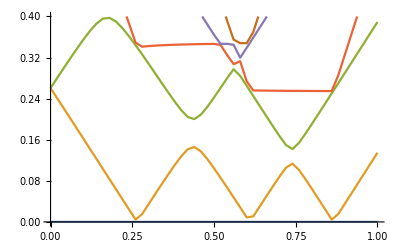

```mathematica
ListPlot[Eϵ,PlotRange->{0.0,2Δ},Joined->True]
```

```mathematica
Iϵ={};
didv={};
dv=0.01;
Eϵ=Table[{},{n,1,2^6}];
For[B=0.0,B≤1.0,B+=0.02,
ϵ={ϵ1,ϵ1,ϵ2,ϵ2,ϵ3,ϵ3};
(*Hamiltonian*)
Hd3=Sum[ϵ[[i]](dd[[i]].d[[i]]-d[[i]].dd[[i]]),{i,1,6}]+t Sum[dd[[i+2]].d[[i]]+dd[[i]].d[[i+2]],{i,1,4}]+B Sum[dd[[i+1]].d[[i]]+dd[[i]].d[[i+1]],{i,1,5,2}]+α Sum[dd[[i]].d[[i+3]]+dd[[i+3]].d[[i]]-dd[[i+1]].d[[i+2]]-dd[[i+2]].d[[i+1]],{i,1,4,2}]+Δ Sum[dd[[i+1]].dd[[i]]+d[[i]].d[[i+1]],{i,1,5,2}]+U Sum[dd[[i]].d[[i]].dd[[i+1]].d[[i+1]],{i,1,5,2}];{e,Ψ}=Transpose[Sort[Transpose[Eigensystem[Hd3]]]];

For[n=1,n≤2^6,n++,
Eϵ[[n]]=Join[Eϵ[[n]],{{B,e[[n]]-e[[1]]}}];
];



For[ev=-0.02,ev≤0.4,ev+=0.01,

(*Tempeture and the fermi distribution*)
kb=8.6 10^-5; (*ev/K*)(*need to translate into eigenvalue units*)
T=kb*100;
f[ϵ_]:=1/(ⅇ^(ϵ/T)+1);
(*Hopping to right and left leads*)
tL={-0.1,-0.1,0.0,0.0,0.0,0.0};
tR={0.0,0.0,0.0,0.0,-0.1,-0.1};
bkt[n_,M_,m_]:=Conjugate[Ψ[[n]]].M.Ψ[[m]];
P[ev_]:=Block[{ptp,M,V,PuN,P1,P,Γ,ΓgainL,ΓlossL,ΓgainR,ΓlossR},
ΓgainL=Table[f[e[[n]]-e[[m]]-ev]Sum[tL[[i]]^2 Abs[bkt[n,dd[[i]],m]]^2,{i,1,2}],{n,1,2^6},{m,1,2^6}];
ΓlossL=Table[(1-f[e[[m]]-e[[n]]-ev])Sum[tL[[i]]^2 Abs[bkt[n,d[[i]],m]]^2,{i,1,2}],{n,1,2^6},{m,1,2^6}];

ΓgainR=Table[f[e[[n]]-e[[m]]+ev]Sum[tR[[i]]^2 Abs[bkt[n,dd[[i]],m]]^2,{i,5,6}],{n,1,2^6},{m,1,2^6}];
ΓlossR=Table[(1-f[e[[m]]-e[[n]]+ev])Sum[tR[[i]]^2 Abs[bkt[n,d[[i]],m]]^2,{i,5,6}],{n,1,2^6},{m,1,2^6}];
Γ=ΓgainL+ΓlossL+ΓgainR+ΓlossR;
M=Table[Γ[[n,m]]-Sum[KroneckerDelta[n,m]Γ[[l,n]],{l,1,2^6}],{n,2,2^6},{m,2,2^6}];
V=Table[-Γ[[n,1]],{n,2,2^6}];
PuN=Inverse[M].V;
P1=1/(1+Sum[PuN[[n]],{n,1,2^6-1}]);
ptp=Join[{P1},PuN*P1];

ptp
];
Ii[ev_]:=Block[{itp,M,V,PuN,P1,P,Γ,ΓgainL,ΓlossL,ΓgainR,ΓlossR},
ΓgainL=Table[f[e[[n]]-e[[m]]-ev]Sum[tL[[i]]^2 Abs[bkt[n,dd[[i]],m]]^2,{i,1,2}],{n,1,2^6},{m,1,2^6}];
ΓlossL=Table[(1-f[e[[m]]-e[[n]]-ev])Sum[tL[[i]]^2 Abs[bkt[n,d[[i]],m]]^2,{i,1,2}],{n,1,2^6},{m,1,2^6}];

ΓgainR=Table[f[e[[n]]-e[[m]]+ev]Sum[tR[[i]]^2 Abs[bkt[n,dd[[i]],m]]^2,{i,5,6}],{n,1,2^6},{m,1,2^6}];
ΓlossR=Table[(1-f[e[[m]]-e[[n]]+ev])Sum[tR[[i]]^2 Abs[bkt[n,d[[i]],m]]^2,{i,5,6}],{n,1,2^6},{m,1,2^6}];
Γ=ΓgainL+ΓlossL+ΓgainR+ΓlossR;
M=Table[Γ[[n,m]]-Sum[KroneckerDelta[n,m]Γ[[l,n]],{l,1,2^6}],{n,2,2^6},{m,2,2^6}];
V=Table[-Γ[[n,1]],{n,2,2^6}];
PuN=Inverse[M].V;
P1=1/(1+Sum[PuN[[n]],{n,1,2^6-1}]);
P=Join[{P1},PuN*P1];
itp=Sum[P[[n]]*Sum[ΓgainL[[m,n]]+ΓlossR[[m,n]]-ΓlossL[[m,n]]-ΓgainR[[m,n]],{m,1,2^6}],{n,1,2^6}];

itp
];
Itp=Ii[ev];
Idv=Ii[ev+dv];
didv0=(Idv-Itp)/dv;
Iϵ=Join[Iϵ,{{B,ev,Itp}}];
didv=Join[didv,{{B,ev,didv0}}];
Print[{B,ev,Itp,didv0}];
];
];
```

{0.,-0.02,-3.75486×10^-15,2.6859×10^-13}

{0.,-0.01,-1.06896×10^-15,1.069×10^-13}

{0.,0.,3.12301×10^-20,1.06914×10^-13}

{0.,0.01,1.06918×10^-15,2.68531×10^-13}

{0.,0.02,3.75448×10^-15,8.36106×10^-13}

{0.,0.03,1.21155×10^-14,2.66745×10^-12}

{0.,0.04,3.87901×10^-14,8.53036×10^-12}

{0.,0.05,1.24094×10^-13,2.72867×10^-11}

{0.,0.06,3.96961×10^-13,8.72856×10^-11}

{0.,0.07,1.26982×10^-12,2.79213×10^-10}

{0.,0.08,4.06195×10^-12,8.93161×10^-10}

{0.,0.09,1.29936×10^-11,2.85709×10^-9}

{0.,0.1,4.15644×10^-11,9.13938×10^-9}

{0.,0.11,1.32958×10^-10,2.92355×10^-8}

{0.,0.12,4.25313×10^-10,9.35199×10^-8}

{0.,0.13,1.36051×10^-9,2.99155×10^-7}

{0.,0.14,4.35207×10^-9,9.56949×10^-7}

{0.,0.15,1.39216×10^-8,3.0611×10^-6}

{0.,0.16,4.45326×10^-8,9.79163×10^-6}

{0.,0.17,1.42449×10^-7,0.0000313183}

{0.,0.18,4.55632×10^-7,0.000100145}

{0.,0.19,1.45708×10^-6,0.000319963}

{0.,0.2,4.65671×10^-6,0.00101959}

{0.,0.21,0.0000148526,0.00322196}

{0.,0.22,0.0000470723,0.00991952}

{0.,0.23,0.000146267,0.0282736}

{0.,0.24,0.000429003,0.0661799}

{0.,0.25,0.0010908,0.107823}

{0.,0.26,0.00216903,0.119675}

{0.,0.27,0.00336578,0.100092}

{0.,0.28,0.0043667,0.0588857}

{0.,0.29,0.00495556,0.0247074}

{0.,0.3,0.00520263,0.00861184}

{0.,0.31,0.00528875,0.00279117}

{0.,0.32,0.00531666,0.000882683}

{0.,0.33,0.00532549,0.000276992}

{0.,0.34,0.00532826,0.0000867617}

{0.,0.35,0.00532913,0.0000271785}

{0.,0.36,0.0053294,8.51064×10^-6}

{0.,0.37,0.00532949,2.66277×10^-6}

{0.,0.38,0.00532951,8.32676×10^-7}

{0.,0.39,0.00532952,2.60335×10^-7}

{0.,0.4,0.00532952,8.13953×10^-8}

{0.02,-0.02,-1.8274×10^-14,1.30704×10^-12}

{0.02,-0.01,-5.20363×10^-15,5.20339×10^-13}

{0.02,0.,-2.32935×10^-19,5.20476×10^-13}

{0.02,0.01,5.20452×10^-15,1.30694×10^-12}

{0.02,0.02,1.82739×10^-14,4.06905×10^-12}

{0.02,0.03,5.89644×10^-14,1.29813×10^-11}

{0.02,0.04,1.88777×10^-13,4.15141×10^-11}

{0.02,0.05,6.03918×10^-13,1.32794×10^-10}

{0.02,0.06,1.93186×10^-12,4.24787×10^-10}

{0.02,0.07,6.17973×10^-12,1.35883×10^-9}

{0.02,0.08,1.9768×10^-11,4.34668×10^-9}

{0.02,0.09,6.32348×10^-11,1.39044×10^-8}

{0.02,0.1,2.02279×10^-10,4.4478×10^-8}

{0.02,0.11,6.47058×10^-10,1.42278×10^-7}

{0.02,0.12,2.06984×10^-9,4.55125×10^-7}

{0.02,0.13,6.62109×10^-9,1.45587×10^-6}

{0.02,0.14,2.11798×10^-8,4.65699×10^-6}

{0.02,0.15,6.77496×10^-8,0.0000148959}

{0.02,0.16,2.16709×10^-7,0.0000476387}

{0.02,0.17,6.93096×10^-7,0.000152276}

{0.02,0.18,2.21585×10^-6,0.000485952}

{0.02,0.19,7.07537×10^-6,0.00154276}

{0.02,0.2,0.000022503,0.00481816}

{0.02,0.21,0.0000706846,0.0143088}

{0.02,0.22,0.000213773,0.0368538}

{0.02,0.23,0.000582311,0.0682155}

{0.02,0.24,0.00126447,0.0742802}

{0.02,0.25,0.00200727,0.0508061}

{0.02,0.26,0.00251533,0.039521}

{0.02,0.27,0.00291054,0.0547187}

{0.02,0.28,0.00345773,0.0739519}

{0.02,0.29,0.00419725,0.0625372}

{0.02,0.3,0.00482262,0.0323291}

{0.02,0.31,0.00514591,0.0123299}

{0.02,0.32,0.00526921,0.00412618}

{0.02,0.33,0.00531047,0.00131858}

{0.02,0.34,0.00532366,0.000415094}

{0.02,0.35,0.00532781,0.000130071}

{0.02,0.36,0.00532911,0.0000407193}

{0.02,0.37,0.00532951,0.0000127493}

{0.02,0.38,0.00532964,3.99047×10^-6}

{0.02,0.39,0.00532968,1.24822×10^-6}

{0.02,0.4,0.00532969,3.90329×10^-7}

{0.04,-0.02,-1.75762×10^-13,1.25709×10^-11}

{0.04,-0.01,-5.00538×10^-14,5.00535×10^-12}

{0.04,0.,-2.8392×10^-19,5.00545×10^-12}

{0.04,0.01,5.00542×10^-14,1.25709×10^-11}

{0.04,0.02,1.75763×10^-13,3.91367×10^-11}

{0.04,0.03,5.6713×10^-13,1.24856×10^-10}

{0.04,0.04,1.81569×10^-12,3.99291×10^-10}

{0.04,0.05,5.8086×10^-12,1.27724×10^-9}

{0.04,0.06,1.8581×10^-11,4.08568×10^-9}

{0.04,0.07,5.94377×10^-11,1.30695×10^-8}

{0.04,0.08,1.90132×10^-10,4.18072×10^-8}

{0.04,0.09,6.08204×10^-10,1.33735×10^-7}

{0.04,0.1,1.94555×10^-9,4.27796×10^-7}

{0.04,0.11,6.22351×10^-9,1.36845×10^-6}

{0.04,0.12,1.9908×10^-8,4.37736×10^-6}

{0.04,0.13,6.36815×10^-8,0.0000140015}

{0.04,0.14,2.03697×10^-7,0.0000447789}

{0.04,0.15,6.51486×10^-7,0.00014314}

{0.04,0.16,2.08288×10^-6,0.000456851}

{0.04,0.17,6.65139×10^-6,0.00145092}

{0.04,0.18,0.0000211606,0.00453672}

{0.04,0.19,0.0000665278,0.0135208}

{0.04,0.2,0.000201736,0.035148}

{0.04,0.21,0.000553216,0.0661745}

{0.04,0.22,0.00121496,0.0725817}

{0.04,0.23,0.00194078,0.0446328}

{0.04,0.24,0.00238711,0.0187325}

{0.04,0.25,0.00257443,0.00728194}

{0.04,0.26,0.00264725,0.0049348}

{0.04,0.27,0.0026966,0.00936741}

{0.04,0.28,0.00279027,0.0240091}

{0.04,0.29,0.00303036,0.0513364}

{0.04,0.3,0.00354373,0.0726913}

{0.04,0.31,0.00427064,0.0595198}

{0.04,0.32,0.00486584,0.0298004}

{0.04,0.33,0.00516384,0.0111832}

{0.04,0.34,0.00527567,0.00371976}

{0.04,0.35,0.00531287,0.00118627}

{0.04,0.36,0.00532473,0.000373193}

{0.04,0.37,0.00532847,0.000116916}

{0.04,0.38,0.00532964,0.0000365977}

{0.04,0.39,0.00533,0.0000114576}

{0.04,0.4,0.00533012,3.58607×10^-6}

{0.06,-0.02,-1.72086×10^-12,1.23079×10^-10}

{0.06,-0.01,-4.9007×10^-13,4.90071×10^-11}

{0.06,0.,4.80639×10^-19,4.9007×10^-11}

{0.06,0.01,4.9007×10^-13,1.23079×10^-10}

{0.06,0.02,1.72086×10^-12,3.83181×10^-10}

{0.06,0.03,5.55267×10^-12,1.22245×10^-9}

{0.06,0.04,1.77771×10^-11,3.90939×10^-9}

{0.06,0.05,5.6871×10^-11,1.25052×10^-8}

{0.06,0.06,1.81923×10^-10,4.00022×10^-8}

{0.06,0.07,5.81945×10^-10,1.27961×10^-7}

{0.06,0.08,1.86155×10^-9,4.09326×10^-7}

{0.06,0.09,5.95481×10^-9,1.30936×10^-6}

{0.06,0.1,1.90484×10^-8,4.18837×10^-6}

{0.06,0.11,6.09321×10^-8,0.0000133971}

{0.06,0.12,1.94903×10^-7,0.0000428461}

{0.06,0.13,6.23364×10^-7,0.000136966}

{0.06,0.14,1.99302×10^-6,0.000437188}

{0.06,0.15,6.3649×10^-6,0.0013889}

{0.06,0.16,0.0000202539,0.00434699}

{0.06,0.17,0.0000637238,0.0129932}

{0.06,0.18,0.000193656,0.0340437}

{0.06,0.19,0.000534092,0.0651613}

{0.06,0.2,0.00118571,0.0731051}

{0.06,0.21,0.00191676,0.0457655}

{0.06,0.22,0.00237441,0.019155}

{0.06,0.23,0.00256596,0.00664743}

{0.06,0.24,0.00263244,0.00217799}

{0.06,0.25,0.00265422,0.000780428}

{0.06,0.26,0.00266202,0.000539504}

{0.06,0.27,0.00266742,0.00110536}

{0.06,0.28,0.00267847,0.00327748}

{0.06,0.29,0.00271124,0.00979966}

{0.06,0.3,0.00280924,0.026276}

{0.06,0.31,0.003072,0.0545826}

{0.06,0.32,0.00361783,0.0731486}

{0.06,0.33,0.00434931,0.0563498}

{0.06,0.34,0.00491281,0.0270347}

{0.06,0.35,0.00518316,0.00994614}

{0.06,0.36,0.00528262,0.00328444}

{0.06,0.37,0.00531546,0.00104495}

{0.06,0.38,0.00532591,0.000328494}

{0.06,0.39,0.0053292,0.000102913}

{0.06,0.4,0.00533023,0.000032288}

{0.08,-0.02,-1.69405×10^-11,1.21162×10^-9}

{0.08,-0.01,-4.82435×10^-12,4.82435×10^-10}

{0.08,0.,-1.01264×10^-19,4.82435×10^-10}

{0.08,0.01,4.82435×10^-12,1.21162×10^-9}

{0.08,0.02,1.69405×10^-11,3.7721×10^-9}

{0.08,0.03,5.46615×10^-11,1.2034×10^-8}

{0.08,0.04,1.75001×10^-10,3.84847×10^-8}

{0.08,0.05,5.59849×10^-10,1.23104×10^-7}

{0.08,0.06,1.79088×10^-9,3.93788×10^-7}

{0.08,0.07,5.72876×10^-9,1.25966×10^-6}

{0.08,0.08,1.83254×10^-8,4.02938×10^-6}

{0.08,0.09,5.86191×10^-8,0.0000128885}

{0.08,0.1,1.87505×10^-7,0.0000412201}

{0.08,0.11,5.99706×10^-7,0.000131771}

{0.08,0.12,1.91742×10^-6,0.000420642}

{0.08,0.13,6.12384×10^-6,0.00133669}

{0.08,0.14,0.0000194907,0.00418698}

{0.08,0.15,0.0000613604,0.0125459}

{0.08,0.16,0.000186819,0.0330936}

{0.08,0.17,0.000517755,0.0642529}

{0.08,0.18,0.00116028,0.0735447}

{0.08,0.19,0.00189573,0.0468465}

{0.08,0.2,0.0023642,0.0197928}

{0.08,0.21,0.00256212,0.00688581}

{0.08,0.22,0.00263098,0.0022295}

{0.08,0.23,0.00265328,0.00070579}

{0.08,0.24,0.00266034,0.000224771}

{0.08,0.25,0.00266258,0.0000811002}

{0.08,0.26,0.00266339,0.0000597668}

{0.08,0.27,0.00266399,0.000128658}

{0.08,0.28,0.00266528,0.000391112}

{0.08,0.29,0.00266919,0.00123564}

{0.08,0.3,0.00268155,0.00385787}

{0.08,0.31,0.00272012,0.0114779}

{0.08,0.32,0.0028349,0.0299732}

{0.08,0.33,0.00313464,0.0590013}

{0.08,0.34,0.00372465,0.0729487}

{0.08,0.35,0.00445414,0.0517023}

{0.08,0.36,0.00497116,0.0234833}

{0.08,0.37,0.00520599,0.00843295}

{0.08,0.38,0.00529032,0.00276245}

{0.08,0.39,0.00531795,0.000877354}

{0.08,0.4,0.00532672,0.000275811}

{0.1,-0.02,-1.67426×10^-10,1.19746×10^-8}

{0.1,-0.01,-4.76798×10^-11,4.76798×10^-9}

{0.1,0.,-1.14619×10^-19,4.76798×10^-9}

{0.1,0.01,4.76798×10^-11,1.19746×10^-8}

{0.1,0.02,1.67426×10^-10,3.72803×10^-8}

{0.1,0.03,5.40229×10^-10,1.18934×10^-7}

{0.1,0.04,1.72957×10^-9,3.8035×10^-7}

{0.1,0.05,5.53307×10^-9,1.21664×10^-6}

{0.1,0.06,1.76995×10^-8,3.89177×10^-6}

{0.1,0.07,5.66172×10^-8,0.0000124484}

{0.1,0.08,1.81101×10^-7,0.0000398128}

{0.1,0.09,5.79229×10^-7,0.000127275}

{0.1,0.1,1.85198×10^-6,0.000406318}

{0.1,0.11,5.91516×10^-6,0.00129146}

{0.1,0.12,0.0000188298,0.00404818}

{0.1,0.13,0.0000593116,0.0121561}

{0.1,0.14,0.000180873,0.0322547}

{0.1,0.15,0.00050342,0.0634188}

{0.1,0.16,0.00113761,0.0739065}

{0.1,0.17,0.00187667,0.0478275}

{0.1,0.18,0.00235495,0.0203861}

{0.1,0.19,0.00255881,0.00711723}

{0.1,0.2,0.00262998,0.00230689}

{0.1,0.21,0.00265305,0.0007295}

{0.1,0.22,0.00266034,0.000228916}

{0.1,0.23,0.00266263,0.0000717756}

{0.1,0.24,0.00266335,0.0000228703}

{0.1,0.25,0.00266358,8.50792×10^-6}

{0.1,0.26,0.00266367,7.00243×10^-6}

{0.1,0.27,0.00266374,0.0000160792}

{0.1,0.28,0.0026639,0.0000494451}

{0.1,0.29,0.00266439,0.000157401}

{0.1,0.3,0.00266596,0.000501787}

{0.1,0.31,0.00267098,0.00158971}

{0.1,0.32,0.00268688,0.00493397}

{0.1,0.33,0.00273622,0.0144099}

{0.1,0.34,0.00288032,0.0359454}

{0.1,0.35,0.00323977,0.0648295}

{0.1,0.36,0.00388807,0.0708343}

{0.1,0.37,0.00459641,0.0446315}

{0.1,0.38,0.00504272,0.01888}

{0.1,0.39,0.00523152,0.00657846}

{0.1,0.4,0.00529731,0.00213126}

{0.12,-0.02,-1.65948×10^-9,1.18689×10^-7}

{0.12,-0.01,-4.7259×10^-10,4.7259×10^-8}

{0.12,0.,4.87874×10^-20,4.7259×10^-8}

{0.12,0.01,4.7259×10^-10,1.18689×10^-7}

{0.12,0.02,1.65948×10^-9,3.69513×10^-7}

{0.12,0.03,5.35461×10^-9,1.17883×10^-6}

{0.12,0.04,1.71429×10^-8,3.76984×10^-6}

{0.12,0.05,5.48414×10^-8,0.0000120581}

{0.12,0.06,1.75423×10^-7,0.0000385647}

{0.12,0.07,5.6107×10^-7,0.000123288}

{0.12,0.08,1.79395×10^-6,0.000393613}

{0.12,0.09,5.73008×10^-6,0.00125133}

{0.12,0.1,0.0000182434,0.00392487}

{0.12,0.11,0.000057492,0.0118085}

{0.12,0.12,0.000175577,0.0314977}

{0.12,0.13,0.000490554,0.0626405}

{0.12,0.14,0.00111696,0.0742117}

{0.12,0.15,0.00185908,0.0487361}

{0.12,0.16,0.00234644,0.0209461}

{0.12,0.17,0.0025559,0.0073373}

{0.12,0.18,0.00262927,0.00238095}

{0.12,0.19,0.00265308,0.000753187}

{0.12,0.2,0.00266061,0.000236334}

{0.12,0.21,0.00266298,0.0000739692}

{0.12,0.22,0.00266372,0.0000231382}

{0.12,0.23,0.00266395,7.25349×10^-6}

{0.12,0.24,0.00266402,2.32963×10^-6}

{0.12,0.25,0.00266404,9.26649×10^-7}

{0.12,0.26,0.00266405,9.2428×10^-7}

{0.12,0.27,0.00266406,2.31906×10^-6}

{0.12,0.28,0.00266409,7.21904×10^-6}

{0.12,0.29,0.00266416,0.0000230275}

{0.12,0.3,0.00266439,0.0000736099}

{0.12,0.31,0.00266512,0.000235132}

{0.12,0.32,0.00266748,0.0007488}

{0.12,0.33,0.00267496,0.00236166}

{0.12,0.34,0.00269858,0.00722963}

{0.12,0.35,0.00277088,0.0203167}

{0.12,0.36,0.00297404,0.046334}

{0.12,0.37,0.00343738,0.071255}

{0.12,0.38,0.00414993,0.0635392}

{0.12,0.39,0.00478533,0.0338079}

{0.12,0.4,0.0051234,0.0130653}

{0.14,-0.02,-1.64815×10^-8,1.17879×10^-6}

{0.14,-0.01,-4.69366×10^-9,4.69366×10^-7}

{0.14,0.,4.36279×10^-20,4.69366×10^-7}

{0.14,0.01,4.69366×10^-9,1.17879×10^-6}

{0.14,0.02,1.64815×10^-8,3.66984×10^-6}

{0.14,0.03,5.31799×10^-8,0.000011707}

{0.14,0.04,1.7025×10^-7,0.0000374323}

{0.14,0.05,5.44573×10^-7,0.000119667}

{0.14,0.06,1.74124×10^-6,0.000382073}

{0.14,0.07,5.56197×10^-6,0.00121486}

{0.14,0.08,0.0000177106,0.00381269}

{0.14,0.09,0.0000558375,0.0114911}

{0.14,0.1,0.000170748,0.0307995}

{0.14,0.11,0.000478744,0.0619014}

{0.14,0.12,0.00109776,0.0744758}

{0.14,0.13,0.00184252,0.0495962}

{0.14,0.14,0.00233848,0.0214858}

{0.14,0.15,0.00255334,0.00755073}

{0.14,0.16,0.00262884,0.00245293}

{0.14,0.17,0.00265337,0.000776237}

{0.14,0.18,0.00266113,0.000243594}

{0.14,0.19,0.00266357,0.0000762422}

{0.14,0.2,0.00266433,0.0000238433}

{0.14,0.21,0.00266457,7.45497×10^-6}

{0.14,0.22,0.00266465,2.33178×10^-6}

{0.14,0.23,0.00266467,7.32733×10^-7}

{0.14,0.24,0.00266468,2.41154×10^-7}

{0.14,0.25,0.00266468,1.14069×10^-7}

{0.14,0.26,0.00266468,1.59393×10^-7}

{0.14,0.27,0.00266468,4.45634×10^-7}

{0.14,0.28,0.00266469,1.40542×10^-6}

{0.14,0.29,0.0026647,4.48934×10^-6}

{0.14,0.3,0.00266474,0.0000143576}

{0.14,0.31,0.00266489,0.0000459148}

{0.14,0.32,0.00266535,0.000146749}

{0.14,0.33,0.00266681,0.000468151}

{0.14,0.34,0.0026715,0.00148462}

{0.14,0.35,0.00268634,0.00462133}

{0.14,0.36,0.00273256,0.0136056}

{0.14,0.37,0.00286861,0.0345067}

{0.14,0.38,0.00321368,0.0635011}

{0.14,0.39,0.00384869,0.0702847}

{0.14,0.4,0.00455154,0.04454}

{0.16,-0.02,-1.63889×10^-7,0.0000117215}

{0.16,-0.01,-4.66746×10^-8,4.66746×10^-6}

{0.16,0.,-2.62994×10^-19,4.66746×10^-6}

{0.16,0.01,4.66746×10^-8,0.0000117215}

{0.16,0.02,1.63889×10^-7,0.0000364857}

{0.16,0.03,5.28746×10^-7,0.000116332}

{0.16,0.04,1.69206×10^-6,0.000371349}

{0.16,0.05,5.40556×10^-6,0.00118094}

{0.16,0.06,0.0000172149,0.0037082}

{0.16,0.07,0.0000542969,0.0111945}

{0.16,0.08,0.000166242,0.0301409}

{0.16,0.09,0.000467651,0.0611854}

{0.16,0.1,0.00107951,0.0747096}

{0.16,0.11,0.0018266,0.050429}

{0.16,0.12,0.00233089,0.0220173}

{0.16,0.13,0.00255106,0.00776224}

{0.16,0.14,0.00262869,0.00252442}

{0.16,0.15,0.00265393,0.000799144}

{0.16,0.16,0.00266192,0.000250811}

{0.16,0.17,0.00266443,0.0000785036}

{0.16,0.18,0.00266522,0.0000245507}

{0.16,0.19,0.00266546,7.6758×10^-6}

{0.16,0.2,0.00266554,2.39968×10^-6}

{0.16,0.21,0.00266556,7.50307×10^-7}

{0.16,0.22,0.00266557,2.34964×10^-7}

{0.16,0.23,0.00266557,7.47583×10^-8}

{0.16,0.24,0.00266557,2.75463×10^-8}

{0.16,0.25,0.00266557,2.19693×10^-8}

{0.16,0.26,0.00266557,4.95979×10^-8}

{0.16,0.27,0.00266557,1.52192×10^-7}

{0.16,0.28,0.00266557,4.84817×10^-7}

{0.16,0.29,0.00266558,1.55021×10^-6}

{0.16,0.3,0.00266559,4.95857×10^-6}

{0.16,0.31,0.00266564,0.0000158602}

{0.16,0.32,0.0026658,0.0000507196}

{0.16,0.33,0.00266631,0.000162093}

{0.16,0.34,0.00266793,0.000516974}

{0.16,0.35,0.0026731,0.00163816}

{0.16,0.36,0.00268948,0.00508648}

{0.16,0.37,0.00274035,0.0148584}

{0.16,0.38,0.00288893,0.0368325}

{0.16,0.39,0.00325726,0.0641723}

{0.16,0.4,0.00389898,0.0651375}

{0.18,-0.02,-1.62977×10^-6,0.000116545}

{0.18,-0.01,-4.64319×10^-7,0.0000464319}

{0.18,0.,-1.98644×10^-20,0.0000464319}

{0.18,0.01,4.64319×10^-7,0.000116545}

{0.18,0.02,1.62977×10^-6,0.000362187}

{0.18,0.03,5.25163×10^-6,0.00114892}

{0.18,0.04,0.0000167408,0.00360857}

{0.18,0.05,0.0000528265,0.0109105}

{0.18,0.06,0.000161932,0.0295048}

{0.18,0.07,0.00045698,0.0604765}

{0.18,0.08,0.00106175,0.0749211}

{0.18,0.09,0.00181096,0.0512547}

{0.18,0.1,0.0023235,0.0225532}

{0.18,0.11,0.00254904,0.00797681}

{0.18,0.12,0.0026288,0.00259709}

{0.18,0.13,0.00265477,0.000822444}

{0.18,0.14,0.002663,0.000258153}

{0.18,0.15,0.00266558,0.0000808046}

{0.18,0.16,0.00266639,0.0000252706}

{0.18,0.17,0.00266664,7.90088×10^-6}

{0.18,0.18,0.00266672,2.47002×10^-6}

{0.18,0.19,0.00266674,7.72178×10^-7}

{0.18,0.2,0.00266675,2.41428×10^-7}

{0.18,0.21,0.00266675,7.55834×10^-8}

{0.18,0.22,0.00266676,2.39801×10^-8}

{0.18,0.23,0.00266676,8.6216×10^-9}

{0.18,0.24,0.00266676,6.29434×10^-9}

{0.18,0.25,0.00266676,1.34807×10^-8}

{0.18,0.26,0.00266676,4.10427×10^-8}

{0.18,0.27,0.00266676,1.30639×10^-7}

{0.18,0.28,0.00266676,4.1769×10^-7}

{0.18,0.29,0.00266676,1.33605×10^-6}

{0.18,0.3,0.00266678,4.27369×10^-6}

{0.18,0.31,0.00266682,0.0000136697}

{0.18,0.32,0.00266695,0.0000437157}

{0.18,0.33,0.00266739,0.000139719}

{0.18,0.34,0.00266879,0.000445711}

{0.18,0.35,0.00267325,0.00141329}

{0.18,0.36,0.00268738,0.00439723}

{0.18,0.37,0.00273135,0.0129154}

{0.18,0.38,0.00286051,0.0323554}

{0.18,0.39,0.00318406,0.0568801}

{0.18,0.4,0.00375286,0.0575323}

{0.2,-0.02,-0.0000161236,0.00115132}

{0.2,-0.01,-4.61046×10^-6,0.000461046}

{0.2,0.,7.53808×10^-20,0.000461046}

{0.2,0.01,4.61046×10^-6,0.00115132}

{0.2,0.02,0.0000161236,0.00352155}

{0.2,0.03,0.0000513391,0.010635}

{0.2,0.04,0.000157689,0.0288757}

{0.2,0.05,0.000446446,0.0597575}

{0.2,0.06,0.00104402,0.0751159}

{0.2,0.07,0.00179518,0.0520943}

{0.2,0.08,0.00231612,0.0231074}

{0.2,0.09,0.0025472,0.00820009}

{0.2,0.1,0.0026292,0.00267287}

{0.2,0.11,0.00265593,0.00084676}

{0.2,0.12,0.00266439,0.000265817}

{0.2,0.13,0.00266705,0.0000832065}

{0.2,0.14,0.00266788,0.000026022}

{0.2,0.15,0.00266814,8.13586×10^-6}

{0.2,0.16,0.00266823,2.54347×10^-6}

{0.2,0.17,0.00266825,7.95134×10^-7}

{0.2,0.18,0.00266826,2.48577×10^-7}

{0.2,0.19,0.00266826,7.77315×10^-8}

{0.2,0.2,0.00266826,2.43736×10^-8}

{0.2,0.21,0.00266826,7.85555×10^-9}

{0.2,0.22,0.00266826,3.21081×10^-9}

{0.2,0.23,0.00266826,3.41907×10^-9}

{0.2,0.24,0.00266826,8.79513×10^-9}

{0.2,0.25,0.00266826,2.74647×10^-8}

{0.2,0.26,0.00266826,8.7646×10^-8}

{0.2,0.27,0.00266826,2.803×10^-7}

{0.2,0.28,0.00266827,8.96611×10^-7}

{0.2,0.29,0.00266828,2.86805×10^-6}

{0.2,0.3,0.0026683,9.17384×10^-6}

{0.2,0.31,0.0026684,0.0000293393}

{0.2,0.32,0.00266869,0.0000937862}

{0.2,0.33,0.00266963,0.000299337}

{0.2,0.34,0.00267262,0.000950726}

{0.2,0.35,0.00268213,0.00297325}

{0.2,0.36,0.00271186,0.00886641}

{0.2,0.37,0.00280052,0.0230926}

{0.2,0.38,0.00303145,0.0437086}

{0.2,0.39,0.00346854,0.0484092}

{0.2,0.4,0.00395263,0.030044}

{0.22,-0.02,-0.000151889,0.0106912}

{0.22,-0.01,-0.0000449765,0.00449765}

{0.22,0.,-2.03256×10^-19,0.00449765}

{0.22,0.01,0.0000449765,0.0106912}

{0.22,0.02,0.000151889,0.02834}

{0.22,0.03,0.000435289,0.0590403}

{0.22,0.04,0.00102569,0.0753074}

{0.22,0.05,0.00177877,0.0529741}

{0.22,0.06,0.00230851,0.0236975}

{0.22,0.07,0.00254548,0.00843933}

{0.22,0.08,0.00262988,0.00275424}

{0.22,0.09,0.00265742,0.000872886}

{0.22,0.1,0.00266615,0.000274053}

{0.22,0.11,0.00266889,0.0000857879}

{0.22,0.12,0.00266974,0.0000268297}

{0.22,0.13,0.00267001,8.38841×10^-6}

{0.22,0.14,0.0026701,2.62243×10^-6}

{0.22,0.15,0.00267012,8.19816×10^-7}

{0.22,0.16,0.00267013,2.56289×10^-7}

{0.22,0.17,0.00267013,8.01279×10^-8}

{0.22,0.18,0.00267013,2.50772×10^-8}

{0.22,0.19,0.00267014,7.92973×10^-9}

{0.22,0.2,0.00267014,2.76771×10^-9}

{0.22,0.21,0.00267014,1.78898×10^-9}

{0.22,0.22,0.00267014,3.51422×10^-9}

{0.22,0.23,0.00267014,1.05511×10^-8}

{0.22,0.24,0.00267014,3.35354×10^-8}

{0.22,0.25,0.00267014,1.07207×10^-7}

{0.22,0.26,0.00267014,3.42917×10^-7}

{0.22,0.27,0.00267014,1.09692×10^-6}

{0.22,0.28,0.00267015,3.50877×10^-6}

{0.22,0.29,0.00267019,0.0000112229}

{0.22,0.3,0.0026703,0.0000358883}

{0.22,0.31,0.00267066,0.00011468}

{0.22,0.32,0.0026718,0.000365604}

{0.22,0.33,0.00267546,0.00115698}

{0.22,0.34,0.00268703,0.00357737}

{0.22,0.35,0.0027228,0.0103129}

{0.22,0.36,0.00282593,0.024591}

{0.22,0.37,0.00307184,0.0391499}

{0.22,0.38,0.00346334,0.0347864}

{0.22,0.39,0.00381121,0.0181427}

{0.22,0.4,0.00399263,0.00692179}

{0.24,-0.02,-0.000991291,0.0615105}

{0.24,-0.01,-0.000376186,0.0376186}

{0.24,0.,2.71421×10^-19,0.0376186}

{0.24,0.01,0.000376186,0.0615105}

{0.24,0.02,0.000991291,0.0765174}

{0.24,0.03,0.00175647,0.0542431}

{0.24,0.04,0.0022989,0.0244454}

{0.24,0.05,0.00254335,0.00873505}

{0.24,0.06,0.0026307,0.00285418}

{0.24,0.07,0.00265924,0.00090491}

{0.24,0.08,0.00266829,0.000284142}

{0.24,0.09,0.00267113,0.0000889498}

{0.24,0.1,0.00267202,0.0000278189}

{0.24,0.11,0.0026723,8.69772×10^-6}

{0.24,0.12,0.00267239,2.71913×10^-6}

{0.24,0.13,0.00267241,8.50046×10^-7}

{0.24,0.14,0.00267242,2.65738×10^-7}

{0.24,0.15,0.00267243,8.30778×10^-8}

{0.24,0.16,0.00267243,2.59864×10^-8}

{0.24,0.17,0.00267243,8.17247×10^-9}

{0.24,0.18,0.00267243,2.71085×10^-9}

{0.24,0.19,0.00267243,1.34658×10^-9}

{0.24,0.2,0.00267243,2.0176×10^-9}

{0.24,0.21,0.00267243,5.73816×10^-9}

{0.24,0.22,0.00267243,1.81317×10^-8}

{0.24,0.23,0.00267243,5.79306×10^-8}

{0.24,0.24,0.00267243,1.85289×10^-7}

{0.24,0.25,0.00267243,5.927×10^-7}

{0.24,0.26,0.00267244,1.89592×10^-6}

{0.24,0.27,0.00267245,6.06435×10^-6}

{0.24,0.28,0.00267252,0.0000193948}

{0.24,0.29,0.00267271,0.000061999}

{0.24,0.3,0.00267333,0.000197896}

{0.24,0.31,0.00267531,0.000628679}

{0.24,0.32,0.00268159,0.00196747}

{0.24,0.33,0.00270127,0.00587931}

{0.24,0.34,0.00276006,0.0153944}

{0.24,0.35,0.00291401,0.0294283}

{0.24,0.36,0.00320829,0.0329656}

{0.24,0.37,0.00353794,0.0206144}

{0.24,0.38,0.00374409,0.00862255}

{0.24,0.39,0.00383031,0.00298785}

{0.24,0.4,0.00386019,0.000966315}

{0.26,-0.02,-0.00214706,0.0817878}

{0.26,-0.01,-0.00132918,0.132918}

{0.26,0.,2.20267×10^-19,0.132918}

{0.26,0.01,0.00132918,0.0817878}

{0.26,0.02,0.00214706,0.0348172}

{0.26,0.03,0.00249523,0.0122058}

{0.26,0.04,0.00261729,0.00396408}

{0.26,0.05,0.00265693,0.00125441}

{0.26,0.06,0.00266947,0.000393649}

{0.26,0.07,0.00267341,0.000123208}

{0.26,0.08,0.00267464,0.0000385307}

{0.26,0.09,0.00267503,0.0000120466}

{0.26,0.1,0.00267515,3.76605×10^-6}

{0.26,0.11,0.00267518,1.17733×10^-6}

{0.26,0.12,0.0026752,3.6805×10^-7}

{0.26,0.13,0.0026752,1.1506×10^-7}

{0.26,0.14,0.0026752,3.59794×10^-8}

{0.26,0.15,0.0026752,1.12798×10^-8}

{0.26,0.16,0.0026752,3.62906×10^-9}

{0.26,0.17,0.0026752,1.46354×10^-9}

{0.26,0.18,0.0026752,1.5101×10^-9}

{0.26,0.19,0.0026752,3.83907×10^-9}

{0.26,0.2,0.0026752,1.19706×10^-8}

{0.26,0.21,0.0026752,3.81949×10^-8}

{0.26,0.22,0.0026752,1.22149×10^-7}

{0.26,0.23,0.0026752,3.90725×10^-7}

{0.26,0.24,0.00267521,1.24985×10^-6}

{0.26,0.25,0.00267522,3.99788×10^-6}

{0.26,0.26,0.00267526,0.0000127866}

{0.26,0.27,0.00267539,0.0000408818}

{0.26,0.28,0.0026758,0.000130564}

{0.26,0.29,0.0026771,0.000415515}

{0.26,0.3,0.00268126,0.00130765}

{0.26,0.31,0.00269433,0.00397459}

{0.26,0.32,0.00273408,0.0109074}

{0.26,0.33,0.00284315,0.0231112}

{0.26,0.34,0.00307426,0.0301289}

{0.26,0.35,0.00337555,0.0216388}

{0.26,0.36,0.00359194,0.00980209}

{0.26,0.37,0.00368996,0.00350931}

{0.26,0.38,0.00372506,0.00114742}

{0.26,0.39,0.00373653,0.000363878}

{0.26,0.4,0.00374017,0.000114316}

{0.28,-0.02,-0.00167185,0.0851039}

{0.28,-0.01,-0.000820806,0.0820806}

{0.28,0.,-7.75168×10^-20,0.0820806}

{0.28,0.01,0.000820806,0.0851039}

{0.28,0.02,0.00167185,0.0593286}

{0.28,0.03,0.00226513,0.0269903}

{0.28,0.04,0.00253503,0.00970252}

{0.28,0.05,0.00263206,0.00317761}

{0.28,0.06,0.00266384,0.00100823}

{0.28,0.07,0.00267392,0.000316662}

{0.28,0.08,0.00267708,0.0000991376}

{0.28,0.09,0.00267808,0.0000310058}

{0.28,0.1,0.00267839,9.69421×10^-6}

{0.28,0.11,0.00267848,3.03067×10^-6}

{0.28,0.12,0.00267851,9.47446×10^-7}

{0.28,0.13,0.00267852,2.96209×10^-7}

{0.28,0.14,0.00267853,9.26748×10^-8}

{0.28,0.15,0.00267853,2.92148×10^-8}

{0.28,0.16,0.00267853,9.91188×10^-9}

{0.28,0.17,0.00267853,5.59034×10^-9}

{0.28,0.18,0.00267853,9.71838×10^-9}

{0.28,0.19,0.00267853,2.85353×10^-8}

{0.28,0.2,0.00267853,9.04819×10^-8}

{0.28,0.21,0.00267853,2.89186×10^-7}

{0.28,0.22,0.00267853,9.24969×10^-7}

{0.28,0.23,0.00267854,2.95869×10^-6}

{0.28,0.24,0.00267857,9.46321×10^-6}

{0.28,0.25,0.00267867,0.0000302591}

{0.28,0.26,0.00267897,0.0000966694}

{0.28,0.27,0.00267993,0.000307958}

{0.28,0.28,0.00268301,0.000972266}

{0.28,0.29,0.00269274,0.00298442}

{0.28,0.3,0.00272258,0.008423}

{0.28,0.31,0.00280681,0.0190606}

{0.28,0.32,0.00299742,0.0276602}

{0.28,0.33,0.00327402,0.0221558}

{0.28,0.34,0.00349558,0.0107544}

{0.28,0.35,0.00360312,0.00396779}

{0.28,0.36,0.0036428,0.00131121}

{0.28,0.37,0.00365591,0.00041725}

{0.28,0.38,0.00366008,0.00013117}

{0.28,0.39,0.0036614,0.0000410803}

{0.28,0.4,0.00366181,0.0000128582}

{0.3,-0.02,-0.000410406,0.0280118}

{0.3,-0.01,-0.000130288,0.0130288}

{0.3,0.,6.57037×10^-20,0.0130288}

{0.3,0.01,0.000130288,0.0280118}

{0.3,0.02,0.000410406,0.0578839}

{0.3,0.03,0.000989244,0.075917}

{0.3,0.04,0.00174841,0.0550273}

{0.3,0.05,0.00229869,0.0250724}

{0.3,0.06,0.00254941,0.00899871}

{0.3,0.07,0.0026394,0.00294481}

{0.3,0.08,0.00266885,0.000934104}

{0.3,0.09,0.00267819,0.000293355}

{0.3,0.1,0.00268112,0.0000918382}

{0.3,0.11,0.00268204,0.0000287227}

{0.3,0.12,0.00268233,8.9804×10^-6}

{0.3,0.13,0.00268242,2.8077×10^-6}

{0.3,0.14,0.00268244,8.78351×10^-7}

{0.3,0.15,0.00268245,2.76556×10^-7}

{0.3,0.16,0.00268246,9.2761×10^-8}

{0.3,0.17,0.00268246,4.91703×10^-8}

{0.3,0.18,0.00268246,7.98984×10^-8}

{0.3,0.19,0.00268246,2.31389×10^-7}

{0.3,0.2,0.00268246,7.32608×10^-7}

{0.3,0.21,0.00268247,2.34106×10^-6}

{0.3,0.22,0.00268249,7.48714×10^-6}

{0.3,0.23,0.00268257,0.0000239418}

{0.3,0.24,0.0026828,0.0000765031}

{0.3,0.25,0.00268357,0.000243878}

{0.3,0.26,0.00268601,0.000771601}

{0.3,0.27,0.00269372,0.00238417}

{0.3,0.28,0.00271757,0.00685937}

{0.3,0.29,0.00278616,0.0162714}

{0.3,0.3,0.00294887,0.0256485}

{0.3,0.31,0.00320536,0.022513}

{0.3,0.32,0.00343049,0.0116339}

{0.3,0.33,0.00354683,0.00441737}

{0.3,0.34,0.003591,0.00147507}

{0.3,0.35,0.00360575,0.000471003}

{0.3,0.36,0.00361046,0.000148229}

{0.3,0.37,0.00361195,0.0000464356}

{0.3,0.38,0.00361241,0.0000145263}

{0.3,0.39,0.00361256,4.54347×10^-6}

{0.3,0.4,0.0036126,1.42499×10^-6}

{0.32,-0.02,-0.0000496337,0.0035321}

{0.32,-0.01,-0.0000143126,0.00143126}

{0.32,0.,-2.54025×10^-19,0.00143126}

{0.32,0.01,0.0000143126,0.0035321}

{0.32,0.02,0.0000496337,0.0104227}

{0.32,0.03,0.000153861,0.0283614}

{0.32,0.04,0.000437475,0.0593087}

{0.32,0.05,0.00103056,0.0757825}

{0.32,0.06,0.00178839,0.0533817}

{0.32,0.07,0.0023222,0.0238989}

{0.32,0.08,0.00256119,0.00851389}

{0.32,0.09,0.00264633,0.0027789}

{0.32,0.1,0.00267412,0.000880732}

{0.32,0.11,0.00268293,0.00027652}

{0.32,0.12,0.00268569,0.000086561}

{0.32,0.13,0.00268656,0.0000270731}

{0.32,0.14,0.00268683,8.46969×10^-6}

{0.32,0.15,0.00268691,2.66438×10^-6}

{0.32,0.16,0.00268694,8.85839×10^-7}

{0.32,0.17,0.00268695,4.46174×10^-7}

{0.32,0.18,0.00268695,6.80875×10^-7}

{0.32,0.19,0.00268696,1.94464×10^-6}

{0.32,0.2,0.00268698,6.14711×10^-6}

{0.32,0.21,0.00268704,0.0000196352}

{0.32,0.22,0.00268724,0.0000627451}

{0.32,0.23,0.00268787,0.000200119}

{0.32,0.24,0.00268987,0.000634172}

{0.32,0.25,0.00269621,0.00196937}

{0.32,0.26,0.0027159,0.00575035}

{0.32,0.27,0.00277341,0.0141627}

{0.32,0.28,0.00291503,0.0239415}

{0.32,0.29,0.00315445,0.0228339}

{0.32,0.3,0.00338279,0.0125394}

{0.32,0.31,0.00350818,0.00490261}

{0.32,0.32,0.00355721,0.00165502}

{0.32,0.33,0.00357376,0.000530421}

{0.32,0.34,0.00357906,0.000167226}

{0.32,0.35,0.00358073,0.0000525479}

{0.32,0.36,0.00358126,0.00001653}

{0.32,0.37,0.00358143,5.19495×10^-6}

{0.32,0.38,0.00358148,1.62926×10^-6}

{0.32,0.39,0.00358149,5.12984×10^-7}

{0.32,0.4,0.0035815,1.70505×10^-7}

{0.34,-0.02,-5.35691×10^-6,0.000382932}

{0.34,-0.01,-1.5276×10^-6,0.00015276}

{0.34,0.,6.40547×10^-20,0.00015276}

{0.34,0.01,1.5276×10^-6,0.000382932}

{0.34,0.02,5.35691×10^-6,0.00118523}

{0.34,0.03,0.0000172092,0.00371226}

{0.34,0.04,0.0000543318,0.0112094}

{0.34,0.05,0.000166426,0.0302233}

{0.34,0.06,0.000468659,0.0615455}

{0.34,0.07,0.00108411,0.075502}

{0.34,0.08,0.00183913,0.0511845}

{0.34,0.09,0.00235098,0.0224032}

{0.34,0.1,0.00257501,0.00790645}

{0.34,0.11,0.00265408,0.00257224}

{0.34,0.12,0.0026798,0.000814378}

{0.34,0.13,0.00268794,0.000255615}

{0.34,0.14,0.0026905,0.0000800522}

{0.34,0.15,0.0026913,0.0000251756}

{0.34,0.16,0.00269155,8.32074×10^-6}

{0.34,0.17,0.00269163,4.03934×10^-6}

{0.34,0.18,0.00269167,5.86256×10^-6}

{0.34,0.19,0.00269173,0.0000165429}

{0.34,0.2,0.0026919,0.0000521874}

{0.34,0.21,0.00269242,0.000166305}

{0.34,0.22,0.00269408,0.000527673}

{0.34,0.23,0.00269936,0.00164565}

{0.34,0.24,0.00271582,0.00486672}

{0.34,0.25,0.00276448,0.0123922}

{0.34,0.26,0.00288841,0.0223632}

{0.34,0.27,0.00311204,0.0231711}

{0.34,0.28,0.00334375,0.0135754}

{0.34,0.29,0.0034795,0.00548427}

{0.34,0.3,0.00353435,0.00187459}

{0.34,0.31,0.00355309,0.000603253}

{0.34,0.32,0.00355912,0.000190323}

{0.34,0.33,0.00356103,0.0000596694}

{0.34,0.34,0.00356162,0.0000186711}

{0.34,0.35,0.00356181,5.84093×10^-6}

{0.34,0.36,0.00356187,1.8339×10^-6}

{0.34,0.37,0.00356189,5.97788×10^-7}

{0.34,0.38,0.00356189,2.6087×10^-7}

{0.34,0.39,0.0035619,2.81898×10^-7}

{0.34,0.4,0.0035619,5.05078×10^-7}

{0.36,-0.02,-5.89396×10^-7,0.0000421522}

{0.36,-0.01,-1.67874×10^-7,0.0000167874}

{0.36,0.,-1.7408×10^-19,0.0000167874}

{0.36,0.01,1.67874×10^-7,0.0000421522}

{0.36,0.02,5.89396×10^-7,0.000131148}

{0.36,0.03,1.90087×10^-6,0.000417543}

{0.36,0.04,6.0763×10^-6,0.00132666}

{0.36,0.05,0.0000193429,0.00415712}

{0.36,0.06,0.0000609141,0.0124716}

{0.36,0.07,0.00018563,0.0330069}

{0.36,0.08,0.000515699,0.0645416}

{0.36,0.09,0.00116112,0.0746248}

{0.36,0.1,0.00190736,0.0479574}

{0.36,0.11,0.00238694,0.0203621}

{0.36,0.12,0.00259056,0.00709777}

{0.36,0.13,0.00266154,0.00229945}

{0.36,0.14,0.00268453,0.00072738}

{0.36,0.15,0.0026918,0.000229379}

{0.36,0.16,0.0026941,0.0000755665}

{0.36,0.17,0.00269485,0.0000357216}

{0.36,0.18,0.00269521,0.0000498171}

{0.36,0.19,0.00269571,0.000138928}

{0.36,0.2,0.0026971,0.000435186}

{0.36,0.21,0.00270145,0.00136087}

{0.36,0.22,0.00271506,0.00407383}

{0.36,0.23,0.0027558,0.010722}

{0.36,0.24,0.00286302,0.0207191}

{0.36,0.25,0.00307021,0.0235577}

{0.36,0.26,0.00330578,0.0149188}

{0.36,0.27,0.00345497,0.00628295}

{0.36,0.28,0.0035178,0.00218276}

{0.36,0.29,0.00353963,0.00070608}

{0.36,0.3,0.00354669,0.000223034}

{0.36,0.31,0.00354892,0.0000699334}

{0.36,0.32,0.00354962,0.000021882}

{0.36,0.33,0.00354984,6.8438×10^-6}

{0.36,0.34,0.00354991,2.14139×10^-6}

{0.36,0.35,0.00354993,6.71632×10^-7}

{0.36,0.36,0.00354994,2.15308×10^-7}

{0.36,0.37,0.00354994,8.40387×10^-8}

{0.36,0.38,0.00354994,7.97393×10^-8}

{0.36,0.39,0.00354994,1.95956×10^-7}

{0.36,0.4,0.00354994,6.08337×10^-7}

{0.38,-0.02,-6.90864×10^-8,4.94115×10^-6}

{0.38,-0.01,-1.96749×10^-8,1.96749×10^-6}

{0.38,0.,1.39196×10^-19,1.96749×10^-6}

{0.38,0.01,1.96749×10^-8,4.94115×10^-6}

{0.38,0.02,6.90864×10^-8,0.0000153821}

{0.38,0.03,2.22907×10^-7,0.000049061}

{0.38,0.04,7.13517×10^-7,0.000156777}

{0.38,0.05,2.28129×10^-6,0.000500269}

{0.38,0.06,7.28398×10^-6,0.00158786}

{0.38,0.07,0.0000231625,0.0049555}

{0.38,0.08,0.0000727175,0.0146851}

{0.38,0.09,0.000219569,0.0375976}

{0.38,0.1,0.000595545,0.0686018}

{0.38,0.11,0.00128156,0.0721203}

{0.38,0.12,0.00200277,0.0427553}

{0.38,0.13,0.00243032,0.0173799}

{0.38,0.14,0.00260412,0.00595775}

{0.38,0.15,0.00266369,0.00192826}

{0.38,0.16,0.00268298,0.000638908}

{0.38,0.17,0.00268937,0.000297468}

{0.38,0.18,0.00269234,0.000402131}

{0.38,0.19,0.00269636,0.00109666}

{0.38,0.2,0.00270733,0.0032772}

{0.38,0.21,0.0027401,0.00893734}

{0.38,0.22,0.00282947,0.0187316}

{0.38,0.23,0.00301679,0.0240129}

{0.38,0.24,0.00325692,0.0169676}

{0.38,0.25,0.0034266,0.00761054}

{0.38,0.26,0.0035027,0.00271334}

{0.38,0.27,0.00352983,0.000885852}

{0.38,0.28,0.00353869,0.000280742}

{0.38,0.29,0.0035415,0.0000880367}

{0.38,0.3,0.00354238,0.0000273496}

{0.38,0.31,0.00354265,8.33306×10^-6}

{0.38,0.32,0.00354274,2.50082×10^-6}

{0.38,0.33,0.00354276,7.59984×10^-7}

{0.38,0.34,0.00354277,2.40349×10^-7}

{0.38,0.35,0.00354277,9.17811×10^-8}

{0.38,0.36,0.00354277,7.72464×10^-8}

{0.38,0.37,0.00354277,1.7418×10^-7}

{0.38,0.38,0.00354278,5.32373×10^-7}

{0.38,0.39,0.00354278,1.69475×10^-6}

{0.38,0.4,0.0035428,5.41761×10^-6}

{0.4,-0.02,-9.31282×10^-9,6.66069×10^-7}

{0.4,-0.01,-2.65213×10^-9,2.65213×10^-7}

{0.4,0.,1.1556×10^-19,2.65213×10^-7}

{0.4,0.01,2.65213×10^-9,6.66069×10^-7}

{0.4,0.02,9.31282×10^-9,2.07364×10^-6}

{0.4,0.03,3.00492×10^-8,6.61524×10^-6}

{0.4,0.04,9.62016×10^-8,0.0000211534}

{0.4,0.05,3.07735×10^-7,0.000067642}

{0.4,0.06,9.84155×10^-7,0.000216145}

{0.4,0.07,3.1456×10^-6,0.000689058}

{0.4,0.08,0.0000100362,0.00218036}

{0.4,0.09,0.0000318398,0.00673963}

{0.4,0.1,0.0000992361,0.0194116}

{0.4,0.11,0.000293352,0.046174}

{0.4,0.12,0.000755092,0.0731483}

{0.4,0.13,0.00148657,0.0645792}

{0.4,0.14,0.00213237,0.0335276}

{0.4,0.15,0.00246764,0.0128217}

{0.4,0.16,0.00259586,0.00450193}

{0.4,0.17,0.00264088,0.0021284}

{0.4,0.18,0.00266216,0.0027972}

{0.4,0.19,0.00269014,0.00691304}

{0.4,0.2,0.00275927,0.0159059}

{0.4,0.21,0.00291832,0.0244174}

{0.4,0.22,0.0031625,0.0208397}

{0.4,0.23,0.0033709,0.0105611}

{0.4,0.24,0.00347651,0.0039737}

{0.4,0.25,0.00351624,0.00132251}

{0.4,0.26,0.00352947,0.000421826}

{0.4,0.27,0.00353369,0.000132705}

{0.4,0.28,0.00353501,0.0000415633}

{0.4,0.29,0.00353543,0.0000129875}

{0.4,0.3,0.00353556,4.01982×10^-6}

{0.4,0.31,0.0035356,1.15037×10^-6}

{0.4,0.32,0.00353561,1.64474×10^-7}

{0.4,0.33,0.00353561,-1.33371×10^-7}

{0.4,0.34,0.00353561,-8.71375×10^-8}

{0.4,0.35,0.00353561,9.18754×10^-8}

{0.4,0.36,0.00353561,4.65967×10^-7}

{0.4,0.37,0.00353562,1.54351×10^-6}

{0.4,0.38,0.00353563,4.94174×10^-6}

{0.4,0.39,0.00353568,0.0000157935}

{0.4,0.4,0.00353584,0.0000504214}

{0.42,-0.02,-1.78774×10^-9,1.27862×10^-7}

{0.42,-0.01,-5.09115×10^-10,5.09115×10^-8}

{0.42,0.,-2.59885×10^-19,5.09115×10^-8}

{0.42,0.01,5.09115×10^-10,1.27862×10^-7}

{0.42,0.02,1.78774×10^-9,3.9807×10^-7}

{0.42,0.03,5.76844×10^-9,1.26994×10^-6}

{0.42,0.04,1.84678×10^-8,4.06118×10^-6}

{0.42,0.05,5.90796×10^-8,0.0000129899}

{0.42,0.06,1.88978×10^-7,0.0000415434}

{0.42,0.07,6.04412×10^-7,0.000132798}

{0.42,0.08,1.93239×10^-6,0.000423848}

{0.42,0.09,6.17087×10^-6,0.00134616}

{0.42,0.1,0.0000196324,0.00420962}

{0.42,0.11,0.0000617286,0.0125503}

{0.42,0.12,0.000187232,0.032656}

{0.42,0.13,0.000513792,0.0616104}

{0.42,0.14,0.0011299,0.0678167}

{0.42,0.15,0.00180806,0.0420613}

{0.42,0.16,0.00222868,0.0185762}

{0.42,0.17,0.00241444,0.00994024}

{0.42,0.18,0.00251384,0.0127866}

{0.42,0.19,0.00264171,0.0233438}

{0.42,0.2,0.00287514,0.0292725}

{0.42,0.21,0.00316787,0.0205651}

{0.42,0.22,0.00337352,0.00920427}

{0.42,0.23,0.00346556,0.00327897}

{0.42,0.24,0.00349835,0.00107025}

{0.42,0.25,0.00350906,0.000339203}

{0.42,0.26,0.00351245,0.000106498}

{0.42,0.27,0.00351351,0.0000333377}

{0.42,0.28,0.00351385,0.0000104261}

{0.42,0.29,0.00351395,3.2596×10^-6}

{0.42,0.3,0.00351398,1.01851×10^-6}

{0.42,0.31,0.00351399,3.17056×10^-7}

{0.42,0.32,0.003514,9.80065×10^-8}

{0.42,0.33,0.003514,5.31412×10^-8}

{0.42,0.34,0.003514,2.3551×10^-7}

{0.42,0.35,0.003514,1.19583×10^-6}

{0.42,0.36,0.00351401,4.45409×10^-6}

{0.42,0.37,0.00351406,0.0000146546}

{0.42,0.38,0.0035142,0.0000469499}

{0.42,0.39,0.00351467,0.000149343}

{0.42,0.4,0.00351617,0.000468924}

{0.44,-0.02,-8.48361×10^-10,6.06763×10^-8}

{0.44,-0.01,-2.41598×10^-10,2.41598×10^-8}

{0.44,0.,2.04779×10^-19,2.41598×10^-8}

{0.44,0.01,2.41598×10^-10,6.06763×10^-8}

{0.44,0.02,8.48361×10^-10,1.88902×10^-7}

{0.44,0.03,2.73739×10^-9,6.02645×10^-7}

{0.44,0.04,8.76383×10^-9,1.92724×10^-6}

{0.44,0.05,2.80362×10^-8,6.16452×10^-6}

{0.44,0.06,8.96814×10^-8,0.0000197167}

{0.44,0.07,2.86848×10^-7,0.0000630436}

{0.44,0.08,9.17284×10^-7,0.000201391}

{0.44,0.09,2.93119×10^-6,0.000641407}

{0.44,0.1,9.34526×10^-6,0.00202342}

{0.44,0.11,0.0000295794,0.00619592}

{0.44,0.12,0.0000915386,0.0173658}

{0.44,0.13,0.000265196,0.0386582}

{0.44,0.14,0.000651779,0.0546755}

{0.44,0.15,0.00119853,0.0432227}

{0.44,0.16,0.00163076,0.0231574}

{0.44,0.17,0.00186233,0.0163581}

{0.44,0.18,0.00202592,0.0251202}

{0.44,0.19,0.00227712,0.0408882}

{0.44,0.2,0.002686,0.0407023}

{0.44,0.21,0.00309302,0.0232751}

{0.44,0.22,0.00332577,0.00929254}

{0.44,0.23,0.0034187,0.00316214}

{0.44,0.24,0.00345032,0.00101607}

{0.44,0.25,0.00346048,0.000320409}

{0.44,0.26,0.00346368,0.000100438}

{0.44,0.27,0.00346469,0.0000314261}

{0.44,0.28,0.003465,9.83042×10^-6}

{0.44,0.29,0.0034651,3.08492×10^-6}

{0.44,0.3,0.00346513,1.00135×10^-6}

{0.44,0.31,0.00346514,4.312×10^-7}

{0.44,0.32,0.00346515,5.12818×10^-7}

{0.44,0.33,0.00346515,1.36984×10^-6}

{0.44,0.34,0.00346517,4.30006×10^-6}

{0.44,0.35,0.00346521,0.0000137502}

{0.44,0.36,0.00346535,0.0000440617}

{0.44,0.37,0.00346579,0.000140624}

{0.44,0.38,0.00346719,0.000442444}

{0.44,0.39,0.00347162,0.00133849}

{0.44,0.4,0.003485,0.00362229}

{0.46,-0.02,-1.62119×10^-9,1.1595×10^-7}

{0.46,-0.01,-4.61685×10^-10,4.61685×10^-8}

{0.46,0.,-2.63767×10^-20,4.61685×10^-8}

{0.46,0.01,4.61685×10^-10,1.1595×10^-7}

{0.46,0.02,1.62119×10^-9,3.60985×10^-7}

{0.46,0.03,5.23104×10^-9,1.15162×10^-6}

{0.46,0.04,1.67473×10^-8,3.68276×10^-6}

{0.46,0.05,5.35749×10^-8,0.000011779}

{0.46,0.06,1.71365×10^-7,0.0000376654}

{0.46,0.07,5.48019×10^-7,0.000120346}

{0.46,0.08,1.75148×10^-6,0.00038355}

{0.46,0.09,5.58698×10^-6,0.00121257}

{0.46,0.1,0.0000177126,0.00373771}

{0.46,0.11,0.0000550897,0.0106783}

{0.46,0.12,0.000161873,0.0248936}

{0.46,0.13,0.00041081,0.0380494}

{0.46,0.14,0.000791303,0.0323393}

{0.46,0.15,0.0011147,0.0167043}

{0.46,0.16,0.00128174,0.00760955}

{0.46,0.17,0.00135784,0.00674107}

{0.46,0.18,0.00142525,0.0143749}

{0.46,0.19,0.00156899,0.0337531}

{0.46,0.2,0.00190653,0.0559381}

{0.46,0.21,0.00246591,0.0523479}

{0.46,0.22,0.00298938,0.0283521}

{0.46,0.23,0.00327291,0.0110103}

{0.46,0.24,0.00338301,0.00370744}

{0.46,0.25,0.00342008,0.0011871}

{0.46,0.26,0.00343195,0.000373923}

{0.46,0.27,0.00343569,0.000117182}

{0.46,0.28,0.00343687,0.0000366954}

{0.46,0.29,0.00343723,0.0000115881}

{0.46,0.3,0.00343735,3.98733×10^-6}

{0.46,0.31,0.00343739,2.4119×10^-6}

{0.46,0.32,0.00343741,4.47824×10^-6}

{0.46,0.33,0.00343746,0.0000132974}

{0.46,0.34,0.00343759,0.0000421338}

{0.46,0.35,0.00343801,0.000133936}

{0.46,0.36,0.00343935,0.000421027}

{0.46,0.37,0.00344356,0.00127556}

{0.46,0.38,0.00345632,0.00346874}

{0.46,0.39,0.003491,0.00719891}

{0.46,0.4,0.00356299,0.00908768}

{0.48,-0.02,-7.81022×10^-9,5.586×10^-7}

{0.48,-0.01,-2.22422×10^-9,2.22422×10^-7}

{0.48,0.,1.32638×10^-19,2.22422×10^-7}

{0.48,0.01,2.22422×10^-9,5.586×10^-7}

{0.48,0.02,7.81022×10^-9,1.73905×10^-6}

{0.48,0.03,2.52007×10^-8,5.54764×10^-6}

{0.48,0.04,8.06771×10^-8,0.0000177377}

{0.48,0.05,2.58054×10^-7,0.0000567011}

{0.48,0.06,8.25066×10^-7,0.000180994}

{0.48,0.07,2.635×10^-6,0.000575067}

{0.48,0.08,8.38567×10^-6,0.00180051}

{0.48,0.09,0.0000263908,0.00538782}

{0.48,0.1,0.000080269,0.01416}

{0.48,0.11,0.000221869,0.0272791}

{0.48,0.12,0.000494659,0.0308843}

{0.48,0.13,0.000803502,0.0194924}

{0.48,0.14,0.000998426,0.00821663}

{0.48,0.15,0.00108059,0.00293236}

{0.48,0.16,0.00110992,0.0012059}

{0.48,0.17,0.00112198,0.00120165}

{0.48,0.18,0.00113399,0.00295781}

{0.48,0.19,0.00116357,0.00873784}

{0.48,0.2,0.00125095,0.0238801}

{0.48,0.21,0.00148975,0.0504381}

{0.48,0.22,0.00199413,0.0654525}

{0.48,0.23,0.00264866,0.0467965}

{0.48,0.24,0.00311662,0.0211392}

{0.48,0.25,0.00332801,0.00755921}

{0.48,0.26,0.0034036,0.00247058}

{0.48,0.27,0.00342831,0.000783459}

{0.48,0.28,0.00343614,0.000246361}

{0.48,0.29,0.00343861,0.0000782355}

{0.48,0.3,0.00343939,0.0000280235}

{0.48,0.31,0.00343967,0.0000201286}

{0.48,0.32,0.00343987,0.0000425891}

{0.48,0.33,0.0034403,0.00012876}

{0.48,0.34,0.00344159,0.000402907}

{0.48,0.35,0.00344561,0.00122193}

{0.48,0.36,0.00345783,0.00333714}

{0.48,0.37,0.0034912,0.00699412}

{0.48,0.38,0.00356115,0.0089637}

{0.48,0.39,0.00365078,0.006332}

{0.48,0.4,0.0037141,0.00283947}

{0.5,-0.02,-5.48698×10^-8,3.92433×10^-6}

{0.5,-0.01,-1.56265×10^-8,1.56265×10^-6}

{0.5,0.,1.56721×10^-20,1.56265×10^-6}

{0.5,0.01,1.56265×10^-8,3.92433×10^-6}

{0.5,0.02,5.48698×10^-8,0.0000122156}

{0.5,0.03,1.77026×10^-7,0.0000389514}

{0.5,0.04,5.6654×10^-7,0.000124368}

{0.5,0.05,1.81022×10^-6,0.000395795}

{0.5,0.06,5.76817×10^-6,0.00124569}

{0.5,0.07,0.0000182251,0.00378722}

{0.5,0.08,0.0000560972,0.0104005}

{0.5,0.09,0.000160102,0.0220721}

{0.5,0.1,0.000380823,0.0288433}

{0.5,0.11,0.000669256,0.0207619}

{0.5,0.12,0.000876875,0.00941746}

{0.5,0.13,0.000971049,0.00337448}

{0.5,0.14,0.00100479,0.00110688}

{0.5,0.15,0.00101586,0.000361762}

{0.5,0.16,0.00101948,0.00014797}

{0.5,0.17,0.00102096,0.000156217}

{0.5,0.18,0.00102252,0.000399634}

{0.5,0.19,0.00102652,0.00123899}

{0.5,0.2,0.00103891,0.00387033}

{0.5,0.21,0.00107761,0.0115838}

{0.5,0.22,0.00119345,0.0304796}

{0.5,0.23,0.00149825,0.0588677}

{0.5,0.24,0.00208692,0.0668832}

{0.5,0.25,0.00275575,0.0423291}

{0.5,0.26,0.00317905,0.0178209}

{0.5,0.27,0.00335725,0.00619191}

{0.5,0.28,0.00341917,0.00200695}

{0.5,0.29,0.00343924,0.000645163}

{0.5,0.3,0.00344569,0.000237118}

{0.5,0.31,0.00344807,0.000184743}

{0.5,0.32,0.00344991,0.000405215}

{0.5,0.33,0.00345397,0.0011784}

{0.5,0.34,0.00346575,0.0032171}

{0.5,0.35,0.00349792,0.00680338}

{0.5,0.36,0.00356595,0.00884806}

{0.5,0.37,0.00365443,0.00633974}

{0.5,0.38,0.00371783,0.00286757}

{0.5,0.39,0.00374651,0.00102597}

{0.5,0.4,0.00375677,0.000335323}

{0.52,-0.02,-4.50123×10^-7,0.0000321897}

{0.52,-0.01,-1.28227×10^-7,0.0000128227}

{0.52,0.,-1.72841×10^-19,0.0000128227}

{0.52,0.01,1.28227×10^-7,0.0000321897}

{0.52,0.02,4.50123×10^-7,0.000100079}

{0.52,0.03,1.45092×10^-6,0.000317904}

{0.52,0.04,4.62995×10^-6,0.00100282}

{0.52,0.05,0.0000146581,0.00307255}

{0.52,0.06,0.0000453836,0.00862674}

{0.52,0.07,0.000131651,0.0192795}

{0.52,0.08,0.000324446,0.0273946}

{0.52,0.09,0.000598392,0.021459}

{0.52,0.1,0.000812982,0.0102648}

{0.52,0.11,0.00091563,0.00376258}

{0.52,0.12,0.000953256,0.00124054}

{0.52,0.13,0.000965661,0.000394582}

{0.52,0.14,0.000969607,0.000124406}

{0.52,0.15,0.000970851,0.000040213}

{0.52,0.16,0.000971253,0.0000165985}

{0.52,0.17,0.000971419,0.0000180512}

{0.52,0.18,0.0009716,0.0000467749}

{0.52,0.19,0.000972067,0.000146088}

{0.52,0.2,0.000973528,0.000465097}

{0.52,0.21,0.000978179,0.00147582}

{0.52,0.22,0.000992937,0.00460501}

{0.52,0.23,0.00103899,0.01364}

{0.52,0.24,0.00117539,0.034878}

{0.52,0.25,0.00152417,0.0634778}

{0.52,0.26,0.00215895,0.0665108}

{0.52,0.27,0.00282405,0.0393305}

{0.52,0.28,0.00321736,0.015996}

{0.52,0.29,0.00337732,0.00558215}

{0.52,0.3,0.00343314,0.0021286}

{0.52,0.31,0.00345443,0.00167793}

{0.52,0.32,0.00347121,0.00326654}

{0.52,0.33,0.00350387,0.00666345}

{0.52,0.34,0.00357051,0.00874934}

{0.52,0.35,0.003658,0.00635926}

{0.52,0.36,0.00372159,0.00290277}

{0.52,0.37,0.00375062,0.00104265}

{0.52,0.38,0.00376105,0.000341299}

{0.52,0.39,0.00376446,0.000108269}

{0.52,0.4,0.00376554,0.0000339964}

{0.54,-0.02,-3.96356×10^-6,0.000283161}

{0.54,-0.01,-1.13195×10^-6,0.000113195}

{0.54,0.,-2.27958×10^-19,0.000113195}

{0.54,0.01,1.13195×10^-6,0.000283161}

{0.54,0.02,3.96356×10^-6,0.000870781}

{0.54,0.03,0.0000126714,0.00267328}

{0.54,0.04,0.0000394041,0.00760557}

{0.54,0.05,0.00011546,0.0175601}

{0.54,0.06,0.00029106,0.0263805}

{0.54,0.07,0.000554866,0.0219371}

{0.54,0.08,0.000774237,0.0109186}

{0.54,0.09,0.000883423,0.00407426}

{0.54,0.1,0.000924165,0.0013519}

{0.54,0.11,0.000937684,0.000430773}

{0.54,0.12,0.000941992,0.000135483}

{0.54,0.13,0.000943347,0.0000424472}

{0.54,0.14,0.000943771,0.0000133212}

{0.54,0.15,0.000943904,4.30523×10^-6}

{0.54,0.16,0.000943947,1.7941×10^-6}

{0.54,0.17,0.000943965,1.99443×10^-6}

{0.54,0.18,0.000943985,5.2091×10^-6}

{0.54,0.19,0.000944037,0.0000162958}

{0.54,0.2,0.0009442,0.0000519993}

{0.54,0.21,0.00094472,0.000166158}

{0.54,0.22,0.000946382,0.000530037}

{0.54,0.23,0.000951682,0.00168063}

{0.54,0.24,0.000968489,0.0052284}

{0.54,0.25,0.00102077,0.0153475}

{0.54,0.26,0.00117425,0.0383243}

{0.54,0.27,0.00155749,0.0665595}

{0.54,0.28,0.00222308,0.0658276}

{0.54,0.29,0.00288136,0.03794}

{0.54,0.3,0.00326076,0.0175703}

{0.54,0.31,0.00343646,0.0113986}

{0.54,0.32,0.00355045,0.0102986}

{0.54,0.33,0.00365344,0.00697811}

{0.54,0.34,0.00372322,0.00315456}

{0.54,0.35,0.00375476,0.00113214}

{0.54,0.36,0.00376608,0.000370602}

{0.54,0.37,0.00376979,0.000117572}

{0.54,0.38,0.00377097,0.0000369249}

{0.54,0.39,0.00377134,0.0000115597}

{0.54,0.4,0.00377145,3.61457×10^-6}

{0.56,-0.02,-0.0000352184,0.0024926}

{0.56,-0.01,-0.0000102924,0.00102924}

{0.56,0.,1.40725×10^-19,0.00102924}

{0.56,0.01,0.0000102924,0.0024926}

{0.56,0.02,0.0000352184,0.00696124}

{0.56,0.03,0.000104831,0.0163966}

{0.56,0.04,0.000268797,0.0256478}

{0.56,0.05,0.000525275,0.0223226}

{0.56,0.06,0.000748501,0.0114669}

{0.56,0.07,0.00086317,0.00434177}

{0.56,0.08,0.000906588,0.00144833}

{0.56,0.09,0.000921071,0.00046231}

{0.56,0.1,0.000925694,0.000145477}

{0.56,0.11,0.000927149,0.0000455721}

{0.56,0.12,0.000927605,0.0000142561}

{0.56,0.13,0.000927747,4.45929×10^-6}

{0.56,0.14,0.000927792,1.39968×10^-6}

{0.56,0.15,0.000927806,4.55348×10^-7}

{0.56,0.16,0.000927811,1.99233×10^-7}

{0.56,0.17,0.000927812,2.44249×10^-7}

{0.56,0.18,0.000927815,6.58434×10^-7}

{0.56,0.19,0.000927822,2.0678×10^-6}

{0.56,0.2,0.000927842,6.60234×10^-6}

{0.56,0.21,0.000927908,0.0000211139}

{0.56,0.22,0.000928119,0.000067516}

{0.56,0.23,0.000928795,0.000215739}

{0.56,0.24,0.000930952,0.000687726}

{0.56,0.25,0.000937829,0.00217579}

{0.56,0.26,0.000959587,0.00672248}

{0.56,0.27,0.00102681,0.0193479}

{0.56,0.28,0.00122029,0.0461401}

{0.56,0.29,0.00168169,0.0751228}

{0.56,0.3,0.00243292,0.0729377}

{0.56,0.31,0.0031623,0.0439638}

{0.56,0.32,0.00360193,0.0187881}

{0.56,0.33,0.00378982,0.00663023}

{0.56,0.34,0.00385612,0.00215993}

{0.56,0.35,0.00387772,0.000684237}

{0.56,0.36,0.00388456,0.000214798}

{0.56,0.37,0.00388671,0.0000672367}

{0.56,0.38,0.00388738,0.0000210277}

{0.56,0.39,0.00388759,6.57434×10^-6}

{0.56,0.4,0.00388766,2.05525×10^-6}

{0.58,-0.02,-0.000249493,0.0162555}

{0.58,-0.01,-0.0000869385,0.00869385}

{0.58,0.,1.64161×10^-19,0.00869385}

{0.58,0.01,0.0000869385,0.0162555}

{0.58,0.02,0.000249493,0.0253281}

{0.58,0.03,0.000502774,0.0227462}

{0.58,0.04,0.000730236,0.0119839}

{0.58,0.05,0.000850075,0.0045933}

{0.58,0.06,0.000896008,0.00153919}

{0.58,0.07,0.000911399,0.000492046}

{0.58,0.08,0.00091632,0.000154908}

{0.58,0.09,0.000917869,0.0000485336}

{0.58,0.1,0.000918354,0.0000151828}

{0.58,0.11,0.000918506,4.74748×10^-6}

{0.58,0.12,0.000918554,1.48466×10^-6}

{0.58,0.13,0.000918568,4.65517×10^-7}

{0.58,0.14,0.000918573,1.4996×10^-7}

{0.58,0.15,0.000918575,6.10582×10^-8}

{0.58,0.16,0.000918575,6.44432×10^-8}

{0.58,0.17,0.000918576,1.65231×10^-7}

{0.58,0.18,0.000918577,5.15751×10^-7}

{0.58,0.19,0.000918583,1.64574×10^-6}

{0.58,0.2,0.000918599,5.26247×10^-6}

{0.58,0.21,0.000918652,0.0000168258}

{0.58,0.22,0.00091882,0.0000537452}

{0.58,0.23,0.000919357,0.00017113}

{0.58,0.24,0.000921069,0.000539445}

{0.58,0.25,0.000926463,0.00164834}

{0.58,0.26,0.000942947,0.00460182}

{0.58,0.27,0.000988965,0.0103271}

{0.58,0.28,0.00109224,0.0165242}

{0.58,0.29,0.00125748,0.0233978}

{0.58,0.3,0.00149146,0.0416542}

{0.58,0.31,0.001908,0.0669375}

{0.58,0.32,0.00257737,0.0647852}

{0.58,0.33,0.00322523,0.0362412}

{0.58,0.34,0.00358764,0.0143098}

{0.58,0.35,0.00373074,0.00484898}

{0.58,0.36,0.00377923,0.00155589}

{0.58,0.37,0.00379478,0.000490417}

{0.58,0.38,0.00379969,0.000153707}

{0.58,0.39,0.00380123,0.0000480897}

{0.58,0.4,0.00380171,0.0000150373}

{0.6,-0.02,-0.000687184,0.0291397}

{0.6,-0.01,-0.000395788,0.0395788}

{0.6,0.,4.39979×10^-20,0.0395788}

{0.6,0.01,0.000395788,0.0291397}

{0.6,0.02,0.000687184,0.0145408}

{0.6,0.03,0.000832592,0.00550186}

{0.6,0.04,0.000887611,0.00183753}

{0.6,0.05,0.000905986,0.000586861}

{0.6,0.06,0.000911855,0.000184706}

{0.6,0.07,0.000913702,0.000057864}

{0.6,0.08,0.000914281,0.0000181011}

{0.6,0.09,0.000914462,5.6599×10^-6}

{0.6,0.1,0.000914518,1.76979×10^-6}

{0.6,0.11,0.000914536,5.54305×10^-7}

{0.6,0.12,0.000914541,1.76592×10^-7}

{0.6,0.13,0.000914543,6.57888×10^-8}

{0.6,0.14,0.000914544,5.4422×10^-8}

{0.6,0.15,0.000914544,1.25311×10^-7}

{0.6,0.16,0.000914546,3.85598×10^-7}

{0.6,0.17,0.000914549,1.22865×10^-6}

{0.6,0.18,0.000914562,3.92818×10^-6}

{0.6,0.19,0.000914601,0.0000125593}

{0.6,0.2,0.000914727,0.0000401145}

{0.6,0.21,0.000915128,0.000127704}

{0.6,0.22,0.000916405,0.000402306}

{0.6,0.23,0.000920428,0.00122666}

{0.6,0.24,0.000932694,0.00339652}

{0.6,0.25,0.00096666,0.00734824}

{0.6,0.26,0.00104014,0.00992067}

{0.6,0.27,0.00113935,0.00748922}

{0.6,0.28,0.00121424,0.00395093}

{0.6,0.29,0.00125375,0.00304463}

{0.6,0.3,0.0012842,0.00606911}

{0.6,0.31,0.00134489,0.0166572}

{0.6,0.32,0.00151146,0.0405967}

{0.6,0.33,0.00191743,0.0680706}

{0.6,0.34,0.00259813,0.0643321}

{0.6,0.35,0.00324145,0.0350887}

{0.6,0.36,0.00359234,0.013673}

{0.6,0.37,0.00372907,0.00460987}

{0.6,0.38,0.00377517,0.00147668}

{0.6,0.39,0.00378994,0.000465196}

{0.6,0.4,0.00379459,0.000145778}

{0.62,-0.02,-0.00065936,0.0295088}

{0.62,-0.01,-0.000364272,0.0364272}

{0.62,0.,2.85858×10^-20,0.0364272}

{0.62,0.01,0.000364272,0.0295088}

{0.62,0.02,0.00065936,0.0160823}

{0.62,0.03,0.000820183,0.00636506}

{0.62,0.04,0.000883833,0.00216245}

{0.62,0.05,0.000905458,0.000694588}

{0.62,0.06,0.000912404,0.00021901}

{0.62,0.07,0.000914594,0.0000686503}

{0.62,0.08,0.00091528,0.0000214794}

{0.62,0.09,0.000915495,6.71746×10^-6}

{0.62,0.1,0.000915562,2.10323×10^-6}

{0.62,0.11,0.000915583,6.67407×10^-7}

{0.62,0.12,0.00091559,2.40292×10^-7}

{0.62,0.13,0.000915592,1.76364×10^-7}

{0.62,0.14,0.000915594,3.78996×10^-7}

{0.62,0.15,0.000915598,1.15442×10^-6}

{0.62,0.16,0.00091561,3.67419×10^-6}

{0.62,0.17,0.000915646,0.0000117422}

{0.62,0.18,0.000915764,0.0000375049}

{0.62,0.19,0.000916139,0.000119416}

{0.62,0.2,0.000917333,0.000376387}

{0.62,0.21,0.000921097,0.00114945}

{0.62,0.22,0.000932591,0.00319692}

{0.62,0.23,0.00096456,0.00698676}

{0.62,0.24,0.00103443,0.00956863}

{0.62,0.25,0.00113011,0.0072175}

{0.62,0.26,0.00120229,0.00337452}

{0.62,0.27,0.00123603,0.00124029}

{0.62,0.28,0.00124844,0.000460601}

{0.62,0.29,0.00125304,0.000317013}

{0.62,0.3,0.00125621,0.000644564}

{0.62,0.31,0.00126266,0.00192721}

{0.62,0.32,0.00128193,0.00593952}

{0.62,0.33,0.00134133,0.017244}

{0.62,0.34,0.00151377,0.041913}

{0.62,0.35,0.0019329,0.0691068}

{0.62,0.36,0.00262396,0.0639453}

{0.62,0.37,0.00326342,0.0343307}

{0.62,0.38,0.00360672,0.0132748}

{0.62,0.39,0.00373947,0.00446275}

{0.62,0.4,0.0037841,0.00142818}

{0.64,-0.02,-0.000213683,0.0141607}

{0.64,-0.01,-0.0000720765,0.00720765}

{0.64,0.,-3.28782×10^-20,0.00720765}

{0.64,0.01,0.0000720765,0.0141607}

{0.64,0.02,0.000213683,0.0242244}

{0.64,0.03,0.000455928,0.0243646}

{0.64,0.04,0.000699573,0.0139834}

{0.64,0.05,0.000839407,0.00559098}

{0.64,0.06,0.000895317,0.00190353}

{0.64,0.07,0.000914352,0.000611756}

{0.64,0.08,0.00092047,0.000192926}

{0.64,0.09,0.000922399,0.0000604862}

{0.64,0.1,0.000923004,0.0000189554}

{0.64,0.11,0.000923194,6.02462×10^-6}

{0.64,0.12,0.000923254,2.19487×10^-6}

{0.64,0.13,0.000923276,1.68207×10^-6}

{0.64,0.14,0.000923293,3.71112×10^-6}

{0.64,0.15,0.00092333,0.0000113446}

{0.64,0.16,0.000923443,0.0000360757}

{0.64,0.17,0.000923804,0.000114833}

{0.64,0.18,0.000924952,0.000362112}

{0.64,0.19,0.000928573,0.00110758}

{0.64,0.2,0.000939649,0.00309429}

{0.64,0.21,0.000970592,0.00683398}

{0.64,0.22,0.00103893,0.00952171}

{0.64,0.23,0.00113415,0.00730822}

{0.64,0.24,0.00120723,0.0034503}

{0.64,0.25,0.00124173,0.00125759}

{0.64,0.26,0.00125431,0.000414296}

{0.64,0.27,0.00125845,0.000133337}

{0.64,0.28,0.00125979,0.0000473091}

{0.64,0.29,0.00126026,0.0000321286}

{0.64,0.3,0.00126058,0.000065426}

{0.64,0.31,0.00126123,0.000197414}

{0.64,0.32,0.00126321,0.000625835}

{0.64,0.33,0.00126947,0.00198043}

{0.64,0.34,0.00128927,0.00613336}

{0.64,0.35,0.00135061,0.0177678}

{0.64,0.36,0.00152828,0.0428856}

{0.64,0.37,0.00195714,0.0697863}

{0.64,0.38,0.002655,0.0635697}

{0.64,0.39,0.0032907,0.0337385}

{0.64,0.4,0.00362808,0.0129737}

{0.66,-0.02,-0.0000287374,0.00203821}

{0.66,-0.01,-8.35533×10^-6,0.000835533}

{0.66,0.,-8.20519×10^-21,0.000835533}

{0.66,0.01,8.35533×10^-6,0.00203821}

{0.66,0.02,0.0000287374,0.0058126}

{0.66,0.03,0.0000868634,0.0144343}

{0.66,0.04,0.000231207,0.0249243}

{0.66,0.05,0.000480449,0.0244147}

{0.66,0.06,0.000724597,0.0136843}

{0.66,0.07,0.00086144,0.00540486}

{0.66,0.08,0.000915488,0.00183159}

{0.66,0.09,0.000933804,0.000587802}

{0.66,0.1,0.000939682,0.000185578}

{0.66,0.11,0.000941538,0.0000591326}

{0.66,0.12,0.000942129,0.0000215985}

{0.66,0.13,0.000942345,0.0000166598}

{0.66,0.14,0.000942512,0.0000368513}

{0.66,0.15,0.000942881,0.000112275}

{0.66,0.16,0.000944003,0.00035269}

{0.66,0.17,0.00094753,0.00108025}

{0.66,0.18,0.000958333,0.0030335}

{0.66,0.19,0.000988668,0.00678281}

{0.66,0.2,0.0010565,0.00964588}

{0.66,0.21,0.00115295,0.00756254}

{0.66,0.22,0.00122858,0.00361957}

{0.66,0.23,0.00126478,0.00132709}

{0.66,0.24,0.00127805,0.000437579}

{0.66,0.25,0.00128242,0.00013916}

{0.66,0.26,0.00128381,0.0000437901}

{0.66,0.27,0.00128425,0.0000138822}

{0.66,0.28,0.00128439,4.88557×10^-6}

{0.66,0.29,0.00128444,3.26625×10^-6}

{0.66,0.3,0.00128447,6.58286×10^-6}

{0.66,0.31,0.00128454,0.0000198472}

{0.66,0.32,0.00128474,0.0000630901}

{0.66,0.33,0.00128537,0.00020149}

{0.66,0.34,0.00128738,0.00064238}

{0.66,0.35,0.00129381,0.00203343}

{0.66,0.36,0.00131414,0.00629301}

{0.66,0.37,0.00137707,0.0181892}

{0.66,0.38,0.00155896,0.0436519}

{0.66,0.39,0.00199548,0.0702843}

{0.66,0.4,0.00269832,0.0632292}

{0.68,-0.02,-3.26417×10^-6,0.000233252}

{0.68,-0.01,-9.3165×10^-7,0.000093165}

{0.68,0.,-3.24698×10^-20,0.000093165}

{0.68,0.01,9.3165×10^-7,0.000233252}

{0.68,0.02,3.26417×10^-6,0.000719169}

{0.68,0.03,0.0000104559,0.00222562}

{0.68,0.04,0.0000327121,0.0064826}

{0.68,0.05,0.0000975381,0.0158759}

{0.68,0.06,0.000256297,0.0265501}

{0.68,0.07,0.000521798,0.0249909}

{0.68,0.08,0.000771706,0.0135889}

{0.68,0.09,0.000907596,0.00528806}

{0.68,0.1,0.000960476,0.00178489}

{0.68,0.11,0.000978325,0.000581372}

{0.68,0.12,0.000984139,0.000214278}

{0.68,0.13,0.000986282,0.000166382}

{0.68,0.14,0.000987945,0.000365178}

{0.68,0.15,0.000991597,0.00107313}

{0.68,0.16,0.00100233,0.00302121}

{0.68,0.17,0.00103254,0.00686795}

{0.68,0.18,0.00110122,0.0100518}

{0.68,0.19,0.00120174,0.0081252}

{0.68,0.2,0.00128299,0.00396777}

{0.68,0.21,0.00132267,0.00146785}

{0.68,0.22,0.00133735,0.00048554}

{0.68,0.23,0.0013422,0.000154556}

{0.68,0.24,0.00134375,0.0000485927}

{0.68,0.25,0.00134423,0.0000152195}

{0.68,0.26,0.00134438,4.76576×10^-6}

{0.68,0.27,0.00134443,1.50707×10^-6}

{0.68,0.28,0.00134445,5.25458×10^-7}

{0.68,0.29,0.00134445,3.37969×10^-7}

{0.68,0.3,0.00134446,6.61287×10^-7}

{0.68,0.31,0.00134446,1.98409×10^-6}

{0.68,0.32,0.00134448,6.30555×10^-6}

{0.68,0.33,0.00134455,0.0000201556}

{0.68,0.34,0.00134475,0.0000644495}

{0.68,0.35,0.00134539,0.000205946}

{0.68,0.36,0.00134745,0.000656582}

{0.68,0.37,0.00135402,0.00207797}

{0.68,0.38,0.0013748,0.00642666}

{0.68,0.39,0.00143906,0.0185401}

{0.68,0.4,0.00162446,0.0442804}

{0.7,-0.02,-4.03705×10^-7,0.0000288709}

{0.7,-0.01,-1.14996×10^-7,0.0000114996}

{0.7,0.,2.90306×10^-20,0.0000114996}

{0.7,0.01,1.14996×10^-7,0.0000288709}

{0.7,0.02,4.03705×10^-7,0.0000897865}

{0.7,0.03,1.30157×10^-6,0.000285466}

{0.7,0.04,4.15623×10^-6,0.000903064}

{0.7,0.05,0.0000131869,0.00279147}

{0.7,0.06,0.0000411015,0.00804098}

{0.7,0.07,0.000121511,0.0191329}

{0.7,0.08,0.00031284,0.0303277}

{0.7,0.09,0.000616117,0.0267975}

{0.7,0.1,0.000884092,0.0139398}

{0.7,0.11,0.00102349,0.00540279}

{0.7,0.12,0.00107752,0.00212248}

{0.7,0.13,0.00109874,0.00165783}

{0.7,0.14,0.00111532,0.003306}

{0.7,0.15,0.00114838,0.00737868}

{0.7,0.16,0.00122217,0.011289}

{0.7,0.17,0.00133506,0.00963481}

{0.7,0.18,0.00143141,0.00488411}

{0.7,0.19,0.00148025,0.00183799}

{0.7,0.2,0.00149863,0.00061175}

{0.7,0.21,0.00150475,0.000195127}

{0.7,0.22,0.0015067,0.0000613873}

{0.7,0.23,0.00150731,0.0000192286}

{0.7,0.24,0.0015075,6.0149×10^-6}

{0.7,0.25,0.00150756,1.88087×10^-6}

{0.7,0.26,0.00150758,5.88546×10^-7}

{0.7,0.27,0.00150759,1.8568×10^-7}

{0.7,0.28,0.00150759,6.34507×10^-8}

{0.7,0.29,0.00150759,3.71236×10^-8}

{0.7,0.3,0.00150759,6.69071×10^-8}

{0.7,0.31,0.00150759,1.97818×10^-7}

{0.7,0.32,0.00150759,6.27721×10^-7}

{0.7,0.33,0.0015076,2.00638×10^-6}

{0.7,0.34,0.00150762,6.41739×10^-6}

{0.7,0.35,0.00150768,0.0000205259}

{0.7,0.36,0.00150789,0.0000656373}

{0.7,0.37,0.00150855,0.000209739}

{0.7,0.38,0.00151064,0.000668638}

{0.7,0.39,0.00151733,0.00211574}

{0.7,0.4,0.00153849,0.00653986}

{0.72,-0.02,-6.99933×10^-8,5.00598×10^-6}

{0.72,-0.01,-1.99335×10^-8,1.99335×10^-6}

{0.72,0.,8.3182×10^-20,1.99335×10^-6}

{0.72,0.01,1.99335×10^-8,5.00598×10^-6}

{0.72,0.02,6.99933×10^-8,0.0000155829}

{0.72,0.03,2.25822×10^-7,0.000049691}

{0.72,0.04,7.22732×10^-7,0.000158685}

{0.72,0.05,2.30958×10^-6,0.000505279}

{0.72,0.06,7.36236×10^-6,0.00159297}

{0.72,0.07,0.0000232921,0.00486838}

{0.72,0.08,0.0000719759,0.0135698}

{0.72,0.09,0.000207674,0.0298214}

{0.72,0.1,0.000505888,0.0413522}

{0.72,0.11,0.000919409,0.0323633}

{0.72,0.12,0.00124304,0.018309}

{0.72,0.13,0.00142613,0.0146265}

{0.72,0.14,0.0015724,0.0180004}

{0.72,0.15,0.0017524,0.0166626}

{0.72,0.16,0.00191903,0.00928307}

{0.72,0.17,0.00201186,0.00366826}

{0.72,0.18,0.00204854,0.00124372}

{0.72,0.19,0.00206098,0.000399157}

{0.72,0.2,0.00206497,0.000125823}

{0.72,0.21,0.00206623,0.0000394366}

{0.72,0.22,0.00206662,0.0000123384}

{0.72,0.23,0.00206675,3.85814×10^-6}

{0.72,0.24,0.00206678,1.2062×10^-6}

{0.72,0.25,0.0020668,3.771×10^-7}

{0.72,0.26,0.0020668,1.1794×10^-7}

{0.72,0.27,0.0020668,3.70371×10^-8}

{0.72,0.28,0.0020668,1.21143×10^-8}

{0.72,0.29,0.0020668,5.50169×10^-9}

{0.72,0.3,0.0020668,7.20471×10^-9}

{0.72,0.31,0.0020668,1.97974×10^-8}

{0.72,0.32,0.0020668,6.23129×10^-8}

{0.72,0.33,0.0020668,1.99012×10^-7}

{0.72,0.34,0.0020668,6.36507×10^-7}

{0.72,0.35,0.00206681,2.03604×10^-6}

{0.72,0.36,0.00206683,6.51275×10^-6}

{0.72,0.37,0.0020669,0.0000208311}

{0.72,0.38,0.0020671,0.0000666129}

{0.72,0.39,0.00206777,0.000212854}

{0.72,0.4,0.0020699,0.000678534}

{0.74,-0.02,-2.54257×10^-8,1.81848×10^-6}

{0.74,-0.01,-7.24085×10^-9,7.24085×10^-7}

{0.74,0.,-2.19142×10^-19,7.24085×10^-7}

{0.74,0.01,7.24085×10^-9,1.81848×10^-6}

{0.74,0.02,2.54257×10^-8,5.66115×10^-6}

{0.74,0.03,8.20372×10^-8,0.0000180575}

{0.74,0.04,2.62612×10^-7,0.0000577168}

{0.74,0.05,8.3978×10^-7,0.000184305}

{0.74,0.06,2.68283×10^-6,0.000586332}

{0.74,0.07,8.54615×10^-6,0.00184318}

{0.74,0.08,0.0000269779,0.00558407}

{0.74,0.09,0.0000828186,0.0152042}

{0.74,0.1,0.000234861,0.0319764}

{0.74,0.11,0.000554625,0.0440556}

{0.74,0.12,0.00099518,0.0452658}

{0.74,0.13,0.00144784,0.0500079}

{0.74,0.14,0.00194792,0.0472833}

{0.74,0.15,0.00242075,0.0281762}

{0.74,0.16,0.00270251,0.0116023}

{0.74,0.17,0.00281853,0.00399953}

{0.74,0.18,0.00285853,0.00129089}

{0.74,0.19,0.00287144,0.000407657}

{0.74,0.2,0.00287552,0.000127845}

{0.74,0.21,0.00287679,0.0000400058}

{0.74,0.22,0.00287719,0.0000125102}

{0.74,0.23,0.00287732,3.91124×10^-6}

{0.74,0.24,0.00287736,1.22274×10^-6}

{0.74,0.25,0.00287737,3.8225×10^-7}

{0.74,0.26,0.00287737,1.19502×10^-7}

{0.74,0.27,0.00287738,3.73744×10^-8}

{0.74,0.28,0.00287738,1.17368×10^-8}

{0.74,0.29,0.00287738,3.83879×10^-9}

{0.74,0.3,0.00287738,1.74299×10^-9}

{0.74,0.31,0.00287738,2.28166×10^-9}

{0.74,0.32,0.00287738,6.26896×10^-9}

{0.74,0.33,0.00287738,1.97315×10^-8}

{0.74,0.34,0.00287738,6.30175×10^-8}

{0.74,0.35,0.00287738,2.01552×10^-7}

{0.74,0.36,0.00287738,6.44722×10^-7}

{0.74,0.37,0.00287739,2.06234×10^-6}

{0.74,0.38,0.00287741,6.5969×10^-6}

{0.74,0.39,0.00287747,0.0000211002}

{0.74,0.4,0.00287768,0.0000674732}

{0.76,-0.02,-3.96776×10^-8,2.83775×10^-6}

{0.76,-0.01,-1.13001×10^-8,1.13001×10^-6}

{0.76,0.,3.21168×10^-21,1.13001×10^-6}

{0.76,0.01,1.13001×10^-8,2.83775×10^-6}

{0.76,0.02,3.96776×10^-8,8.83271×10^-6}

{0.76,0.03,1.28005×10^-7,0.000028158}

{0.76,0.04,4.09585×10^-7,0.0000898393}

{0.76,0.05,1.30798×10^-6,0.000285243}

{0.76,0.06,4.1604×10^-6,0.000891176}

{0.76,0.07,0.0000130722,0.00264968}

{0.76,0.08,0.000039569,0.00684627}

{0.76,0.09,0.000108032,0.0127597}

{0.76,0.1,0.000235629,0.0140505}

{0.76,0.11,0.000376134,0.00982407}

{0.76,0.12,0.000474375,0.00840458}

{0.76,0.13,0.000558421,0.0149173}

{0.76,0.14,0.000707594,0.0289808}

{0.76,0.15,0.000997402,0.0363082}

{0.76,0.16,0.00136048,0.0252863}

{0.76,0.17,0.00161335,0.0112511}

{0.76,0.18,0.00172586,0.00399807}

{0.76,0.19,0.00176584,0.00130382}

{0.76,0.2,0.00177888,0.00041311}

{0.76,0.21,0.00178301,0.000129691}

{0.76,0.22,0.0017843,0.0000405967}

{0.76,0.23,0.00178471,0.0000126963}

{0.76,0.24,0.00178484,3.96957×10^-6}

{0.76,0.25,0.00178488,1.241×10^-6}

{0.76,0.26,0.00178489,3.87961×10^-7}

{0.76,0.27,0.00178489,1.21284×10^-7}

{0.76,0.28,0.00178489,3.79203×10^-8}

{0.76,0.29,0.00178489,1.18712×10^-8}

{0.76,0.3,0.00178489,3.76495×10^-9}

{0.76,0.31,0.00178489,1.34927×10^-9}

{0.76,0.32,0.00178489,9.72953×10^-10}

{0.76,0.33,0.00178489,2.06722×10^-9}

{0.76,0.34,0.00178489,6.286×10^-9}

{0.76,0.35,0.00178489,2.00058×10^-8}

{0.76,0.36,0.0017849,6.39636×10^-8}

{0.76,0.37,0.0017849,2.046×10^-7}

{0.76,0.38,0.0017849,6.54478×10^-7}

{0.76,0.39,0.0017849,2.09355×10^-6}

{0.76,0.4,0.00178493,6.69672×10^-6}

{0.78,-0.02,-2.41514×10^-7,0.0000172705}

{0.78,-0.01,-6.88091×10^-8,6.88091×10^-6}

{0.78,0.,-1.51556×10^-20,6.88091×10^-6}

{0.78,0.01,6.88091×10^-8,0.0000172705}

{0.78,0.02,2.41514×10^-7,0.0000536647}

{0.78,0.03,7.78161×10^-7,0.000170165}

{0.78,0.04,2.47981×10^-6,0.000533783}

{0.78,0.05,7.81764×10^-6,0.00160768}

{0.78,0.06,0.0000238944,0.00430127}

{0.78,0.07,0.0000669071,0.00861091}

{0.78,0.08,0.000153016,0.0103027}

{0.78,0.09,0.000256044,0.00683738}

{0.78,0.1,0.000324417,0.00299766}

{0.78,0.11,0.000354394,0.00119865}

{0.78,0.12,0.00036638,0.00085872}

{0.78,0.13,0.000374968,0.00174351}

{0.78,0.14,0.000392403,0.00493233}

{0.78,0.15,0.000441726,0.0128834}

{0.78,0.16,0.00057056,0.0247933}

{0.78,0.17,0.000818493,0.028051}

{0.78,0.18,0.001099,0.0176895}

{0.78,0.19,0.0012759,0.00743265}

{0.78,0.2,0.00135022,0.00258003}

{0.78,0.21,0.00137603,0.000834615}

{0.78,0.22,0.00138437,0.000263756}

{0.78,0.23,0.00138701,0.0000827349}

{0.78,0.24,0.00138784,0.0000258916}

{0.78,0.25,0.0013881,8.09676×10^-6}

{0.78,0.26,0.00138818,2.53144×10^-6}

{0.78,0.27,0.0013882,7.91401×10^-7}

{0.78,0.28,0.00138821,2.47408×10^-7}

{0.78,0.29,0.00138821,7.73451×10^-8}

{0.78,0.3,0.00138821,2.41845×10^-8}

{0.78,0.31,0.00138821,7.57741×10^-9}

{0.78,0.32,0.00138821,2.42331×10^-9}

{0.78,0.33,0.00138821,9.31931×10^-10}

{0.78,0.34,0.00138821,8.49132×10^-10}

{0.78,0.35,0.00138821,2.04976×10^-9}

{0.78,0.36,0.00138821,6.34852×10^-9}

{0.78,0.37,0.00138821,2.02428×10^-8}

{0.78,0.38,0.00138821,6.47332×10^-8}

{0.78,0.39,0.00138821,2.07064×10^-7}

{0.78,0.4,0.00138822,6.62355×10^-7}

{0.8,-0.02,-2.04445×10^-6,0.000145983}

{0.8,-0.01,-5.84624×10^-7,0.0000584624}

{0.8,0.,-1.76925×10^-20,0.0000584624}

{0.8,0.01,5.84624×10^-7,0.000145983}

{0.8,0.02,2.04445×10^-6,0.000446435}

{0.8,0.03,6.5088×10^-6,0.00134745}

{0.8,0.04,0.0000199833,0.00365277}

{0.8,0.05,0.0000565111,0.00753254}

{0.8,0.06,0.000131837,0.00941764}

{0.8,0.07,0.000226013,0.00649839}

{0.8,0.08,0.000290997,0.00287429}

{0.8,0.09,0.00031974,0.00102014}

{0.8,0.1,0.000329941,0.000336938}

{0.8,0.11,0.000333311,0.000121356}

{0.8,0.12,0.000334524,0.0000849018}

{0.8,0.13,0.000335373,0.000175976}

{0.8,0.14,0.000337133,0.000529179}

{0.8,0.15,0.000342425,0.00164422}

{0.8,0.16,0.000358867,0.00488586}

{0.8,0.17,0.000407725,0.0126186}

{0.8,0.18,0.000533912,0.0234415}

{0.8,0.19,0.000768327,0.025243}

{0.8,0.2,0.00102076,0.0152641}

{0.8,0.21,0.0011734,0.00626962}

{0.8,0.22,0.00123609,0.0021569}

{0.8,0.23,0.00125766,0.000695613}

{0.8,0.24,0.00126462,0.000219614}

{0.8,0.25,0.00126682,0.000068867}

{0.8,0.26,0.0012675,0.0000215496}

{0.8,0.27,0.00126772,6.73875×10^-6}

{0.8,0.28,0.00126779,2.10685×10^-6}

{0.8,0.29,0.00126781,6.5866×10^-7}

{0.8,0.3,0.00126781,2.05911×10^-7}

{0.8,0.31,0.00126782,6.43726×10^-8}

{0.8,0.32,0.00126782,2.01291×10^-8}

{0.8,0.33,0.00126782,6.30986×10^-9}

{0.8,0.34,0.00126782,2.02768×10^-9}

{0.8,0.35,0.00126782,8.10239×10^-10}

{0.8,0.36,0.00126782,8.17438×10^-10}

{0.8,0.37,0.00126782,2.0601×10^-9}

General::munfl: 1.38811×10^-270 7.79542×10^-39 is too small to represent as a normalized machine number; precision may be lost.

{0.8,0.38,0.00126782,6.41591×10^-9}

General::munfl: 1.38811×10^-270 7.79542×10^-39 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.33942×10^-271 7.79542×10^-39 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.8,0.39,0.00126782,2.04644×10^-8}

{0.8,0.4,0.00126782,6.542×10^-8}

{0.82,-0.02,-0.0000181429,0.00127722}

{0.82,-0.01,-5.37072×10^-6,0.000537072}

{0.82,0.,-2.80334×10^-20,0.000537072}

{0.82,0.01,5.37072×10^-6,0.00127722}

{0.82,0.02,0.0000181429,0.00338969}

{0.82,0.03,0.0000520398,0.00708073}

{0.82,0.04,0.000122847,0.00906921}

{0.82,0.05,0.000213539,0.00640499}

{0.82,0.06,0.000277589,0.00287204}

{0.82,0.07,0.000306309,0.00102384}

{0.82,0.08,0.000316548,0.000334301}

{0.82,0.09,0.000319891,0.000106102}

{0.82,0.1,0.000320952,0.0000337685}

{0.82,0.11,0.00032129,0.0000120279}

{0.82,0.12,0.00032141,8.42273×10^-6}

{0.82,0.13,0.000321494,0.00001754}

{0.82,0.14,0.00032167,0.0000531284}

{0.82,0.15,0.000322201,0.000168614}

{0.82,0.16,0.000323887,0.000534855}

{0.82,0.17,0.000329235,0.00166871}

{0.82,0.18,0.000345923,0.00494131}

{0.82,0.19,0.000395336,0.0126256}

{0.82,0.2,0.000521592,0.0229436}

{0.82,0.21,0.000751028,0.023991}

{0.82,0.22,0.000990937,0.0141603}

{0.82,0.23,0.00113254,0.00574267}

{0.82,0.24,0.00118997,0.00196585}

{0.82,0.25,0.00120963,0.000632936}

{0.82,0.26,0.00121596,0.000199719}

{0.82,0.27,0.00121795,0.0000626177}

{0.82,0.28,0.00121858,0.000019593}

{0.82,0.29,0.00121877,6.12682×10^-6}

{0.82,0.3,0.00121884,1.91552×10^-6}

{0.82,0.31,0.00121885,5.98847×10^-7}

{0.82,0.32,0.00121886,1.87212×10^-7}

{0.82,0.33,0.00121886,5.85276×10^-8}

{0.82,0.34,0.00121886,1.83032×10^-8}

{0.82,0.35,0.00121886,5.74304×10^-9}

{0.82,0.36,0.00121886,1.86228×10^-9}

{0.82,0.37,0.00121886,7.88462×10^-10}

{0.82,0.38,0.00121886,8.64193×10^-10}

{0.82,0.39,0.00121886,2.13278×10^-9}

{0.82,0.4,0.00121886,6.50261×10^-9}

{0.84,-0.02,-0.000116175,0.00721635}

{0.84,-0.01,-0.0000440111,0.00440111}

{0.84,0.,-4.25341×10^-21,0.00440111}

{0.84,0.01,0.0000440111,0.00721635}

{0.84,0.02,0.000116175,0.00901583}

{0.84,0.03,0.000206333,0.00641772}

{0.84,0.04,0.00027051,0.00289944}

{0.84,0.05,0.000299505,0.00103714}

{0.84,0.06,0.000309876,0.00033901}

{0.84,0.07,0.000313266,0.000107497}

{0.84,0.08,0.000314341,0.0000337597}

{0.84,0.09,0.000314679,0.0000105827}

{0.84,0.1,0.000314784,3.3551×10^-6}

{0.84,0.11,0.000314818,1.19413×10^-6}

{0.84,0.12,0.00031483,8.37603×10^-7}

{0.84,0.13,0.000314838,1.747×10^-6}

{0.84,0.14,0.000314856,5.2965×10^-6}

{0.84,0.15,0.000314909,0.0000168473}

{0.84,0.16,0.000315077,0.0000538203}

{0.84,0.17,0.000315615,0.000171713}

{0.84,0.18,0.000317333,0.000544802}

{0.84,0.19,0.000322781,0.00169817}

{0.84,0.2,0.000339762,0.00501389}

{0.84,0.21,0.000389901,0.0127122}

{0.84,0.22,0.000517023,0.0227436}

{0.84,0.23,0.000744459,0.0233014}

{0.84,0.24,0.000977473,0.0135288}

{0.84,0.25,0.00111276,0.00543997}

{0.84,0.26,0.00116716,0.0018561}

{0.84,0.27,0.00118572,0.00059694}

{0.84,0.28,0.00119169,0.000188294}

{0.84,0.29,0.00119357,0.000059029}

{0.84,0.3,0.00119416,0.0000184695}

{0.84,0.31,0.00119435,5.77541×10^-6}

{0.84,0.32,0.00119441,1.80565×10^-6}

{0.84,0.33,0.00119442,5.64505×10^-7}

{0.84,0.34,0.00119443,1.76492×10^-7}

{0.84,0.35,0.00119443,5.52163×10^-8}

{0.84,0.36,0.00119443,1.73383×10^-8}

{0.84,0.37,0.00119443,5.50399×10^-9}

{0.84,0.38,0.00119443,1.80422×10^-9}

{0.84,0.39,0.00119443,7.48902×10^-10}

{0.84,0.4,0.00119443,8.08216×10^-10}

{0.86,-0.02,-0.000249702,0.00950613}

{0.86,-0.01,-0.000154641,0.0154641}

{0.86,0.,9.49426×10^-20,0.0154641}

{0.86,0.01,0.000154641,0.00950613}

{0.86,0.02,0.000249702,0.00404335}

{0.86,0.03,0.000290135,0.00141691}

{0.86,0.04,0.000304305,0.000460103}

{0.86,0.05,0.000308906,0.00014559}

{0.86,0.06,0.000310361,0.0000456873}

{0.86,0.07,0.000310818,0.0000142997}

{0.86,0.08,0.000310961,4.47237×10^-6}

{0.86,0.09,0.000311006,1.39969×10^-6}

{0.86,0.1,0.00031102,4.42092×10^-7}

{0.86,0.11,0.000311024,1.52647×10^-7}

{0.86,0.12,0.000311026,9.39177×10^-8}

{0.86,0.13,0.000311027,1.7714×10^-7}

{0.86,0.14,0.000311029,5.28098×10^-7}

{0.86,0.15,0.000311034,1.67722×10^-6}

{0.86,0.16,0.000311051,5.36096×10^-6}

{0.86,0.17,0.000311104,0.0000171433}

{0.86,0.18,0.000311276,0.000054793}

{0.86,0.19,0.000311824,0.000174811}

{0.86,0.2,0.000313572,0.000554499}

{0.86,0.21,0.000319117,0.00172707}

{0.86,0.22,0.000336388,0.00508754}

{0.86,0.23,0.000387263,0.0128212}

{0.86,0.24,0.000515475,0.0226642}

{0.86,0.25,0.000742117,0.0228621}

{0.86,0.26,0.000970738,0.0131109}

{0.86,0.27,0.00110185,0.00523866}

{0.86,0.28,0.00115423,0.00178308}

{0.86,0.29,0.00117206,0.000572988}

{0.86,0.3,0.00117779,0.000180691}

{0.86,0.31,0.0011796,0.000056641}

{0.86,0.32,0.00118017,0.0000177219}

{0.86,0.33,0.00118035,5.54164×10^-6}

{0.86,0.34,0.0011804,1.73264×10^-6}

{0.86,0.35,0.00118042,5.4175×10^-7}

{0.86,0.36,0.00118042,1.69396×10^-7}

{0.86,0.37,0.00118043,5.29644×10^-8}

{0.86,0.38,0.00118043,1.65638×10^-8}

{0.86,0.39,0.00118043,5.19582×10^-9}

{0.86,0.4,0.00118043,1.68075×10^-9}

{0.88,-0.02,-0.00019089,0.00977725}

{0.88,-0.01,-0.0000931172,0.00931172}

{0.88,0.,-7.40138×10^-20,0.00931172}

{0.88,0.01,0.0000931172,0.00977725}

{0.88,0.02,0.00019089,0.00690868}

{0.88,0.03,0.000259977,0.00316923}

{0.88,0.04,0.000291669,0.00114335}

{0.88,0.05,0.000303102,0.000374922}

{0.88,0.06,0.000306852,0.000119008}

{0.88,0.07,0.000308042,0.0000373826}

{0.88,0.08,0.000308415,0.0000117039}

{0.88,0.09,0.000308533,3.66065×10^-6}

{0.88,0.1,0.000308569,1.14498×10^-6}

{0.88,0.11,0.000308581,3.59387×10^-7}

{0.88,0.12,0.000308584,1.16941×10^-7}

{0.88,0.13,0.000308585,5.124×10^-8}

{0.88,0.14,0.000308586,6.2986×10^-8}

{0.88,0.15,0.000308586,1.69932×10^-7}

{0.88,0.16,0.000308588,5.33721×10^-7}

{0.88,0.17,0.000308594,1.70416×10^-6}

{0.88,0.18,0.000308611,5.44994×10^-6}

{0.88,0.19,0.000308665,0.0000174286}

{0.88,0.2,0.000308839,0.0000557042}

{0.88,0.21,0.000309396,0.000177707}

{0.88,0.22,0.000311173,0.00056357}

{0.88,0.23,0.000316809,0.00175421}

{0.88,0.24,0.000334351,0.00515768}

{0.88,0.25,0.000385928,0.0129335}

{0.88,0.26,0.000515263,0.0226392}

{0.88,0.27,0.000741655,0.0225525}

{0.88,0.28,0.00096718,0.0128065}

{0.88,0.29,0.00109524,0.00509143}

{0.88,0.3,0.00114616,0.00172966}

{0.88,0.31,0.00116346,0.000555465}

{0.88,0.32,0.00116901,0.000175129}

{0.88,0.33,0.00117076,0.0000548941}

{0.88,0.34,0.00117131,0.000017175}

{0.88,0.35,0.00117148,5.37055×10^-6}

{0.88,0.36,0.00117154,1.67907×10^-6}

{0.88,0.37,0.00117155,5.24926×10^-7}

{0.88,0.38,0.00117156,1.64103×10^-7}

{0.88,0.39,0.00117156,5.13031×10^-8}

{0.88,0.4,0.00117156,1.60436×10^-8}

{0.9,-0.02,-0.0000446397,0.0030548}

{0.9,-0.01,-0.0000140917,0.00140917}

{0.9,0.,1.89439×10^-20,0.00140917}

{0.9,0.01,0.0000140917,0.0030548}

{0.9,0.02,0.0000446397,0.00643184}

{0.9,0.03,0.000108958,0.00868872}

{0.9,0.04,0.000195845,0.00648514}

{0.9,0.05,0.000260697,0.00300891}

{0.9,0.06,0.000290786,0.00108835}

{0.9,0.07,0.000301669,0.000357133}

{0.9,0.08,0.000305241,0.000113385}

{0.9,0.09,0.000306374,0.0000356184}

{0.9,0.1,0.000306731,0.0000111518}

{0.9,0.11,0.000306842,3.48799×10^-6}

{0.9,0.12,0.000306877,1.09101×10^-6}

{0.9,0.13,0.000306888,3.42536×10^-7}

{0.9,0.14,0.000306891,1.11742×10^-7}

{0.9,0.15,0.000306893,4.98375×10^-8}

{0.9,0.16,0.000306893,6.32599×10^-8}

{0.9,0.17,0.000306894,1.72296×10^-7}

{0.9,0.18,0.000306895,5.41748×10^-7}

{0.9,0.19,0.000306901,1.72999×10^-6}

{0.9,0.2,0.000306918,5.53258×10^-6}

{0.9,0.21,0.000306973,0.0000176928}

{0.9,0.22,0.00030715,0.0000565475}

{0.9,0.23,0.000307716,0.000180388}

{0.9,0.24,0.00030952,0.000571972}

{0.9,0.25,0.000315239,0.00177939}

{0.9,0.26,0.000333033,0.00522323}

{0.9,0.27,0.000385266,0.0130423}

{0.9,0.28,0.000515689,0.0226406}

{0.9,0.29,0.000742095,0.0223177}

{0.9,0.3,0.000965272,0.0125696}

{0.9,0.31,0.00109097,0.00497663}

{0.9,0.32,0.00114073,0.001688}

{0.9,0.33,0.00115761,0.0005418}

{0.9,0.34,0.00116303,0.000170792}

{0.9,0.35,0.00116474,0.0000535317}

{0.9,0.36,0.00116528,0.0000167484}

{0.9,0.37,0.00116544,5.23713×10^-6}

{0.9,0.38,0.0011655,1.63736×10^-6}

{0.9,0.39,0.00116551,5.11885×10^-7}

{0.9,0.4,0.00116552,1.60026×10^-7}

{0.92,-0.02,-5.07789×10^-6,0.000361546}

{0.92,-0.01,-1.46244×10^-6,0.000146244}

{0.92,0.,-5.26857×10^-21,0.000146244}

{0.92,0.01,1.46244×10^-6,0.000361546}

{0.92,0.02,5.07789×10^-6,0.00107257}

{0.92,0.03,0.0000158036,0.00296242}

{0.92,0.04,0.0000454278,0.00641027}

{0.92,0.05,0.00010953,0.00864308}

{0.92,0.06,0.000195961,0.00641683}

{0.92,0.07,0.00026013,0.00296651}

{0.92,0.08,0.000289795,0.00107132}

{0.92,0.09,0.000300508,0.000351348}

{0.92,0.1,0.000304021,0.000111528}

{0.92,0.11,0.000305137,0.000035033}

{0.92,0.12,0.000305487,0.0000109683}

{0.92,0.13,0.000305597,3.4306×10^-6}

{0.92,0.14,0.000305631,1.07307×10^-6}

{0.92,0.15,0.000305642,3.36946×10^-7}

{0.92,0.16,0.000305645,1.10059×10^-7}

{0.92,0.17,0.000305646,4.95175×10^-8}

{0.92,0.18,0.000305647,6.3819×10^-8}

{0.92,0.19,0.000305647,1.7458×10^-7}

{0.92,0.2,0.000305649,5.49207×10^-7}

{0.92,0.21,0.000305654,1.75389×10^-6}

{0.92,0.22,0.000305672,5.60905×10^-6}

{0.92,0.23,0.000305728,0.0000179373}

{0.92,0.24,0.000305907,0.0000573281}

{0.92,0.25,0.000306481,0.000182869}

{0.92,0.26,0.000308309,0.00057975}

{0.92,0.27,0.000314107,0.00180272}

{0.92,0.28,0.000332134,0.00528417}

{0.92,0.29,0.000384976,0.0131456}

{0.92,0.3,0.000516432,0.0226553}

{0.92,0.31,0.000742985,0.0221301}

{0.92,0.32,0.000964285,0.0123767}

{0.92,0.33,0.00108805,0.004883}

{0.92,0.34,0.00113688,0.00165403}

{0.92,0.35,0.00115342,0.000530659}

{0.92,0.36,0.00115873,0.000167256}

{0.92,0.37,0.0011604,0.0000524211}

{0.92,0.38,0.00116093,0.0000164007}

{0.92,0.39,0.00116109,5.12839×10^-6}

{0.92,0.4,0.00116114,1.60336×10^-6}

{0.94,-0.02,-5.07664×10^-7,0.0000362928}

{0.94,-0.01,-1.44736×10^-7,0.0000144736}

{0.94,0.,-1.27734×10^-20,0.0000144736}

{0.94,0.01,1.44736×10^-7,0.0000362928}

{0.94,0.02,5.07664×10^-7,0.000112439}

{0.94,0.03,1.63205×10^-6,0.000353217}

{0.94,0.04,5.16422×10^-6,0.00107631}

{0.94,0.05,0.0000159273,0.00297695}

{0.94,0.06,0.0000456968,0.00642287}

{0.94,0.07,0.000109925,0.00861562}

{0.94,0.08,0.000196082,0.00636346}

{0.94,0.09,0.000259716,0.00293239}

{0.94,0.1,0.00028904,0.00105753}

{0.94,0.11,0.000299615,0.000346658}

{0.94,0.12,0.000303082,0.000110021}

{0.94,0.13,0.000304182,0.0000345582}

{0.94,0.14,0.000304528,0.0000108195}

{0.94,0.15,0.000304636,3.38403×10^-6}

{0.94,0.16,0.00030467,1.05851×10^-6}

{0.94,0.17,0.00030468,3.32415×10^-7}

{0.94,0.18,0.000304684,1.08702×10^-7}

{0.94,0.19,0.000304685,4.92846×10^-8}

{0.94,0.2,0.000304685,6.43581×10^-8}

{0.94,0.21,0.000304686,1.76706×10^-7}

{0.94,0.22,0.000304688,5.56133×10^-7}

{0.94,0.23,0.000304693,1.77608×10^-6}

{0.94,0.24,0.000304711,5.68004×10^-6}

{0.94,0.25,0.000304768,0.0000181642}

{0.94,0.26,0.000304949,0.0000580526}

{0.94,0.27,0.00030553,0.000185172}

{0.94,0.28,0.000307382,0.00058697}

{0.94,0.29,0.000313251,0.00182439}

{0.94,0.3,0.000331495,0.00534087}

{0.94,0.31,0.000384904,0.0132427}

{0.94,0.32,0.000517331,0.0226766}

{0.94,0.33,0.000744097,0.0219743}

{0.94,0.34,0.000963839,0.0122142}

{0.94,0.35,0.00108598,0.00480414}

{0.94,0.36,0.00113402,0.00162542}

{0.94,0.37,0.00115028,0.000521281}

{0.94,0.38,0.00115549,0.00016428}

{0.94,0.39,0.00115713,0.0000514863}

{0.94,0.4,0.00115765,0.000016108}

{0.96,-0.02,-5.00214×10^-8,3.57747×10^-6}

{0.96,-0.01,-1.42468×10^-8,1.42468×10^-6}

{0.96,0.,-9.25334×10^-21,1.42468×10^-6}

{0.96,0.01,1.42468×10^-8,3.57747×10^-6}

{0.96,0.02,5.00214×10^-8,0.0000111323}

{0.96,0.03,1.61344×10^-7,0.0000354604}

{0.96,0.04,5.15948×10^-7,0.000112849}

{0.96,0.05,1.64444×10^-6,0.000355406}

{0.96,0.06,5.1985×10^-6,0.00108279}

{0.96,0.07,0.0000160264,0.00299129}

{0.96,0.08,0.0000459394,0.00643548}

{0.96,0.09,0.000110294,0.00859336}

{0.96,0.1,0.000196228,0.00631838}

{0.96,0.11,0.000259412,0.00290347}

{0.96,0.12,0.000288446,0.00104584}

{0.96,0.13,0.000298905,0.000342682}

{0.96,0.14,0.000302332,0.000108745}

{0.96,0.15,0.000303419,0.0000341557}

{0.96,0.16,0.000303761,0.0000106933}

{0.96,0.17,0.000303867,3.34456×10^-6}

{0.96,0.18,0.000303901,1.04617×10^-6}

{0.96,0.19,0.000303911,3.28575×10^-7}

{0.96,0.2,0.000303915,1.07558×10^-7}

{0.96,0.21,0.000303916,4.9105×10^-8}

{0.96,0.22,0.000303916,6.48721×10^-8}

{0.96,0.23,0.000303917,1.7869×10^-7}

{0.96,0.24,0.000303919,5.62587×10^-7}

{0.96,0.25,0.000303924,1.79676×10^-6}

{0.96,0.26,0.000303942,5.74618×10^-6}

{0.96,0.27,0.000304,0.0000183757}

{0.96,0.28,0.000304183,0.0000587277}

{0.96,0.29,0.000304771,0.000187318}

{0.96,0.3,0.000306644,0.000593699}

{0.96,0.31,0.000312581,0.00184459}

{0.96,0.32,0.000331027,0.00539376}

{0.96,0.33,0.000384964,0.0133338}

{0.96,0.34,0.000518302,0.0227011}

{0.96,0.35,0.000745313,0.021841}

{0.96,0.36,0.000963724,0.0120739}

{0.96,0.37,0.00108446,0.00473609}

{0.96,0.38,0.00113182,0.00160076}

{0.96,0.39,0.00114783,0.000513196}

{0.96,0.4,0.00115296,0.000161714}

{0.98,-0.02,-4.91906×10^-9,3.51819×10^-7}

{0.98,-0.01,-1.40087×10^-9,1.40087×10^-7}

{0.98,0.,-1.05615×10^-20,1.40087×10^-7}

{0.98,0.01,1.40087×10^-9,3.51819×10^-7}

{0.98,0.02,4.91906×10^-9,1.09526×10^-6}

{0.98,0.03,1.58717×10^-8,3.49363×10^-6}

{0.98,0.04,5.0808×10^-8,0.0000111672}

{0.98,0.05,1.6248×10^-7,0.0000356662}

{0.98,0.06,5.19143×10^-7,0.000113529}

{0.98,0.07,1.65443×10^-6,0.000357512}

{0.98,0.08,5.22955×10^-6,0.00108879}

{0.98,0.09,0.0000161174,0.00300455}

{0.98,0.1,0.0000461629,0.00644757}

{0.98,0.11,0.000110639,0.00857471}

{0.98,0.12,0.000196386,0.00627943}

{0.98,0.13,0.00025918,0.00287843}

{0.98,0.14,0.000287964,0.00103573}

{0.98,0.15,0.000298322,0.000339241}

{0.98,0.16,0.000301714,0.00010764}

{0.98,0.17,0.00030279,0.0000338073}

{0.98,0.18,0.000303129,0.0000105841}

{0.98,0.19,0.000303234,3.31039×10^-6}

{0.98,0.2,0.000303267,1.0355×10^-6}

{0.98,0.21,0.000303278,3.25253×10^-7}

{0.98,0.22,0.000303281,1.06571×10^-7}

{0.98,0.23,0.000303282,4.89634×10^-8}

{0.98,0.24,0.000303283,6.53612×10^-8}

{0.98,0.25,0.000303283,1.80549×10^-7}

{0.98,0.26,0.000303285,5.68626×10^-7}

{0.98,0.27,0.000303291,1.81611×10^-6}

{0.98,0.28,0.000303309,5.80806×10^-6}

{0.98,0.29,0.000303367,0.0000185735}

{0.98,0.3,0.000303553,0.0000593592}

{0.98,0.31,0.000304146,0.000189325}

{0.98,0.32,0.00030604,0.000599993}

{0.98,0.33,0.00031204,0.00186348}

{0.98,0.34,0.000330674,0.00544323}

{0.98,0.35,0.000385107,0.0134193}

{0.98,0.36,0.0005193,0.0227269}

{0.98,0.37,0.000746569,0.0217246}

{0.98,0.38,0.000963815,0.0119506}

{0.98,0.39,0.00108332,0.00467632}

{0.98,0.4,0.00113008,0.00157911}

{1.,-0.02,-4.83428×10^-10,3.45756×10^-8}

{1.,-0.01,-1.37672×10^-10,1.37672×10^-8}

{1.,0.,1.14283×10^-20,1.37672×10^-8}

{1.,0.01,1.37672×10^-10,3.45756×10^-8}

{1.,0.02,4.83428×10^-10,1.07643×10^-7}

{1.,0.03,1.55986×10^-9,3.43405×10^-7}

{1.,0.04,4.99391×10^-9,1.09816×10^-6}

{1.,0.05,1.59755×10^-8,3.51222×10^-6}

{1.,0.06,5.10976×10^-8,0.0000112295}

{1.,0.07,1.63393×10^-7,0.0000358657}

{1.,0.08,5.2205×10^-7,0.00011416}

{1.,0.09,1.66365×10^-6,0.000359458}

{1.,0.1,5.25823×10^-6,0.00109433}

{1.,0.11,0.0000162015,0.00301683}

{1.,0.12,0.0000463699,0.00645907}

{1.,0.13,0.000110961,0.00855871}

{1.,0.14,0.000196548,0.00624519}

{1.,0.15,0.000259,0.00285639}

{1.,0.16,0.000287563,0.00102682}

{1.,0.17,0.000297832,0.000336213}

{1.,0.18,0.000301194,0.000106667}

{1.,0.19,0.000302261,0.0000335007}

{1.,0.2,0.000302596,0.000010488}

{1.,0.21,0.0003027,3.28034×10^-6}

{1.,0.22,0.000302733,1.0261×10^-6}

{1.,0.23,0.000302743,3.22331×10^-7}

{1.,0.24,0.000302747,1.05707×10^-7}

{1.,0.25,0.000302748,4.88497×10^-8}

{1.,0.26,0.000302748,6.58264×10^-8}

{1.,0.27,0.000302749,1.82297×10^-7}

{1.,0.28,0.000302751,5.74296×10^-7}

{1.,0.29,0.000302756,1.83427×10^-6}

{1.,0.3,0.000302775,5.86616×10^-6}

{1.,0.31,0.000302833,0.0000187592}

{1.,0.32,0.000303021,0.0000599522}

{1.,0.33,0.000303621,0.00019121}

{1.,0.34,0.000305533,0.000605903}

{1.,0.35,0.000311592,0.00188121}

{1.,0.36,0.000330404,0.00548965}

{1.,0.37,0.0003853,0.0134997}

{1.,0.38,0.000520297,0.0227529}

{1.,0.39,0.000747826,0.0216211}

{1.,0.4,0.000964037,0.0118406}

```mathematica
ListPlot[Eϵ,PlotRange->{0.0,2Δ}]
```

-Graphics-

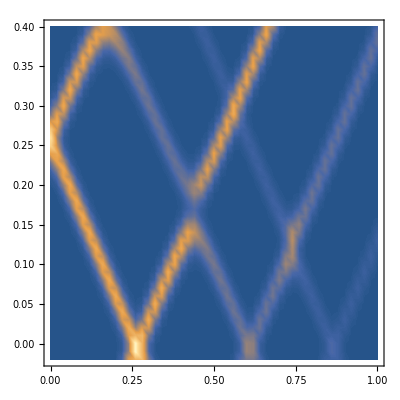

```mathematica
ListContourPlot[didv,PlotRange->All,Contours->100,ContourStyle->None]
```

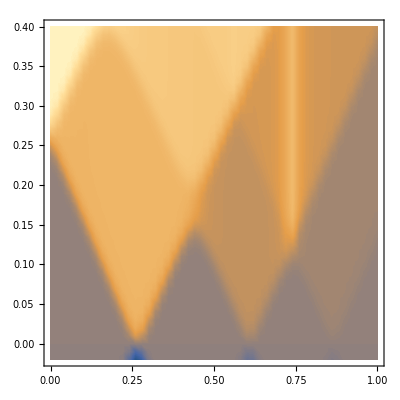

```mathematica
ListContourPlot[Iϵ,PlotRange->All,Contours->100,ContourStyle->None]
```